```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/Dhybrid/math

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ηψ[x_,y_]=D[D[V[x,y], y], y]/V[x,y]//Simplify
```

(4 (3 y^2+M^2 (-1+x^2/ϕc^2)))/(M^4 ((-1+y^2/M^2)^2+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(2 x^2 y^2)/(M^2 ϕc^2)))

```mathematica
Normal[Series[ηψ[ϕc E^ξ,y],{ξ,0,1},{y,0,0}]]
```

(8 ξ)/M^2

## Pi2 = 50

```mathematica
fndata1=Sort[Select[Import["StocDeltaN/Mn_Dhybrid_SR_D=1.dat"],#[[2]]>0&]];
trajdata1=Import["StocDeltaN/traj_Dhybrid_SR_D=1.dat"];
calPdata1=Import["StocDeltaN/calP_Dhybrid_SR_D=1.dat"];
fndata10=Sort[Select[Import["StocDeltaN/Mn_Dhybrid_SR_D=10.dat"],#[[2]]>0&]];
trajdata10=Import["StocDeltaN/traj_Dhybrid_SR_D=10.dat"];
calPdata10=Import["StocDeltaN/calP_Dhybrid_SR_D=10.dat"];
fndata100=Sort[Select[Import["StocDeltaN/Mn_Dhybrid_SR_D=100.dat"],#[[2]]>0&]];
trajdata100=Import["StocDeltaN/traj_Dhybrid_SR_D=100.dat"];
calPdata100=Import["StocDeltaN/calP_Dhybrid_SR_D=100.dat"];
fndata1000=Sort[Select[Import["StocDeltaN/Mn_Dhybrid_SR_D=1000.dat"],#[[2]]>0&]];
trajdata1000=Import["StocDeltaN/traj_Dhybrid_SR_D=1000.dat"];
calPdata1000=Import["StocDeltaN/calP_Dhybrid_SR_D=1000.dat"];
```

```mathematica
f1List1=Table[{fndata1[[i,1]],Log10[fndata1[[i,2]]],fndata1[[i,3]]-UnitStep[-fndata1[[i,3]]]},{i,1,Length[fndata1]}];
g2List1=Table[{fndata1[[i,1]],Log10[fndata1[[i,2]]],Log10[fndata1[[i,4]]]},{i,1,Length[fndata1]}];
phivschi1=Table[{trajdata1[[i,2]],Log10[Abs[trajdata1[[i,3]]]]},{i,Length[trajdata1]}];
Ndata1=Table[{trajdata1[[i,1]],trajdata1[[i,4]]},{i,Length[trajdata1]}];
dN2data1=Table[{trajdata1[[i,1]],trajdata1[[i,5]]},{i,Length[trajdata1]}];
meancalP1=Table[{calPdata1[[i,1]],calPdata1[[i,2]]±calPdata1[[i,3]]},{i,Length[calPdata1]}];
f1List10=Table[{fndata10[[i,1]],Log10[fndata10[[i,2]]],fndata10[[i,3]]-UnitStep[-fndata10[[i,3]]]},{i,1,Length[fndata10]}];
g2List10=Table[{fndata10[[i,1]],Log10[fndata10[[i,2]]],Log10[fndata10[[i,4]]]},{i,1,Length[fndata10]}];
phivschi10=Table[{trajdata10[[i,2]],Log10[Abs[trajdata10[[i,3]]]]},{i,Length[trajdata10]}];
Ndata10=Table[{trajdata10[[i,1]],trajdata10[[i,4]]},{i,Length[trajdata10]}];
dN2data10=Table[{trajdata10[[i,1]],trajdata10[[i,5]]},{i,Length[trajdata10]}];
meancalP10=Table[{calPdata10[[i,1]],calPdata10[[i,2]]±calPdata10[[i,3]]},{i,Length[calPdata10]}];
f1List100=Table[{fndata100[[i,1]],Log10[fndata100[[i,2]]],fndata100[[i,3]]-UnitStep[-fndata100[[i,3]]]},{i,1,Length[fndata100]}];
g2List100=Table[{fndata100[[i,1]],Log10[fndata100[[i,2]]],Log10[fndata100[[i,4]]]},{i,1,Length[fndata100]}];
phivschi100=Table[{trajdata100[[i,2]],Log10[Abs[trajdata100[[i,3]]]]},{i,Length[trajdata100]}];
Ndata100=Table[{trajdata100[[i,1]],trajdata100[[i,4]]},{i,Length[trajdata100]}];
dN2data100=Table[{trajdata100[[i,1]],trajdata100[[i,5]]},{i,Length[trajdata100]}];
meancalP100=Table[{calPdata100[[i,1]],calPdata100[[i,2]]±calPdata100[[i,3]]},{i,Length[calPdata100]}];
f1List1000=Table[{fndata1000[[i,1]],Log10[fndata1000[[i,2]]],fndata1000[[i,3]]-UnitStep[-fndata1000[[i,3]]]},{i,1,Length[fndata1000]}];
g2List1000=Table[{fndata1000[[i,1]],Log10[fndata1000[[i,2]]],Log10[fndata1000[[i,4]]]},{i,1,Length[fndata1000]}];
phivschi1000=Table[{trajdata1000[[i,2]],Log10[Abs[trajdata1000[[i,3]]]]},{i,Length[trajdata1000]}];
Ndata1000=Table[{trajdata1000[[i,1]],trajdata1000[[i,4]]},{i,Length[trajdata1000]}];
dN2data1000=Table[{trajdata1000[[i,1]],trajdata1000[[i,5]]},{i,Length[trajdata1000]}];
meancalP1000=Table[{calPdata1000[[i,1]],calPdata1000[[i,2]]±calPdata1000[[i,3]]},{i,Length[calPdata1000]}];
```

```mathematica
f1int1[ϕ_,logr_]=Interpolation[f1List1][ϕ,logr];
f1int10[ϕ_,logr_]=Interpolation[f1List10][ϕ,logr];
f1int100[ϕ_,logr_]=Interpolation[f1List100][ϕ,logr];
f1int1000[ϕ_,logr_]=Interpolation[f1List1000][ϕ,logr];
g2int1[ϕ_,logr_]=Interpolation[g2List1][ϕ,logr];
g2int10[ϕ_,logr_]=Interpolation[g2List10][ϕ,logr];
g2int100[ϕ_,logr_]=Interpolation[g2List100][ϕ,logr];
g2int1000[ϕ_,logr_]=Interpolation[g2List1000][ϕ,logr];
```

```mathematica
As=2.189 10^-9;
Π2=50;
M=0.1;
ϕc=0.1Sqrt[2];
μ2=11;
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

35355.3

2.07404×10^-16

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

1.96975×10^-9 √Dw

Log[50768./(√Dw)]

```mathematica
N1[Dw_]=(Sqrt[χ2[Dw]]M ϕc^(1/2)μ1^(1/2))/2
N2[Dw_]=(M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2[Dw]])
```

3.53553 √Log[50768./(√Dw)]

1.76777/(√Log[50768./(√Dw)])

```mathematica
ξk[NN_,Dw_]=-(N1[Dw]+N2[Dw]-NN)/(ϕc μ1);
χk[NN_,Dw_]=(4ϕc μ1 ξk[NN,Dw]^2)/M^2;
ψk[NN_,Dw_]=ψ0[Dw] Exp[χk[NN,Dw]];
```

```mathematica
calPCG[NN_,Dw_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2[Dw] ψk[NN,Dw]^2);
```

```mathematica
Ncontour1=Show[ContourPlot[f1int1[ϕ,logr],{ϕ,0.1409,0.142},{logr,-10,-3},FrameLabel->{{"log_10(r/M_Pl)",None},{"ϕ/M_Pl",D==1}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->{{0,{Thick,Dashed}},2,5,10,15,20,25,30,35},MaxRecursion->5],
ListPlot[phivschi1,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{ϕc E^ξk[NN,1],Log10[ψk[NN,1]]},{NN,0,N1[1]+N2[1]},PlotStyle->{Red,Dotted}]];
```

```mathematica
dN2contour1=Show[ContourPlot[g2int1[ϕ,logr],{ϕ,0.1409,0.142},{logr,-10,-3},FrameLabel->{{"log_10(r/M_Pl)",None},{"ϕ/M_Pl",D==1}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,-1}],MaxRecursion->5],ListPlot[phivschi1,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{ϕc E^ξk[NN,1],Log10[ψk[NN,1]]},{NN,0,N1[1]+N2[1]},PlotStyle->{Red,Dotted}]];
```

```mathematica
Ncontour10=Show[ContourPlot[f1int10[ϕ,logr],{ϕ,0.1409,0.142},{logr,-10,-3},FrameLabel->{{"log_10(r/M_Pl)",None},{"ϕ/M_Pl",D==10}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->{{0,{Thick,Dashed}},2,5,10,15,20,25,30,35},MaxRecursion->5],
ListPlot[phivschi10,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{ϕc E^ξk[NN,10],Log10[ψk[NN,10]]},{NN,0,N1[10]+N2[10]},PlotStyle->{Red,Dotted}]];
```

```mathematica
dN2contour10=Show[ContourPlot[g2int10[ϕ,logr],{ϕ,0.1409,0.142},{logr,-10,-3},FrameLabel->{{"log_10(r/M_Pl)",None},{"ϕ/M_Pl",D==10}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,-2}],MaxRecursion->5],ListPlot[phivschi10,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{ϕc E^ξk[NN,10],Log10[ψk[NN,10]]},{NN,0,N1[10]+N2[10]},PlotStyle->{Red,Dotted}]];
```

```mathematica
Ncontour100=Show[ContourPlot[f1int100[ϕ,logr],{ϕ,0.1409,0.142},{logr,-10,-3},FrameLabel->{{"log_10(r/M_Pl)",None},{"ϕ/M_Pl",D==100}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->{{0,{Thick,Dashed}},2,5,10,15,20,25,30,35},MaxRecursion->5],
ListPlot[phivschi100,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{ϕc E^ξk[NN,100],Log10[ψk[NN,100]]},{NN,0,N1[100]+N2[100]},PlotStyle->{Red,Dotted}]];
```

```mathematica
dN2contour100=Show[ContourPlot[g2int100[ϕ,logr],{ϕ,0.1409,0.142},{logr,-10,-3},FrameLabel->{{"log_10(r/M_Pl)",None},{"ϕ/M_Pl",D==100}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,-3}],MaxRecursion->5],ListPlot[phivschi100,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{ϕc E^ξk[NN,100],Log10[ψk[NN,100]]},{NN,0,N1[100]+N2[100]},PlotStyle->{Red,Dotted}]];
```

```mathematica
Ncontour1000=Show[ContourPlot[f1int1000[ϕ,logr],{ϕ,0.1409,0.142},{logr,-10,-3},FrameLabel->{{"log_10(r/M_Pl)",None},{"ϕ/M_Pl",D==1000}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->{{0,{Thick,Dashed}},2,5,10,15,20,25,30,35},MaxRecursion->5],
ListPlot[phivschi1000,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{ϕc E^ξk[NN,1000],Log10[ψk[NN,1000]]},{NN,0,N1[1000]+N2[1000]},PlotStyle->{Red,Dotted}]];
```

```mathematica
dN2contour1000=Show[ContourPlot[g2int1000[ϕ,logr],{ϕ,0.1409,0.142},{logr,-10,-3},FrameLabel->{{"log_10(r/M_Pl)",None},{"ϕ/M_Pl",D==1000}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,-4}],MaxRecursion->5],ListPlot[phivschi1000,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{ϕc E^ξk[NN,1000],Log10[ψk[NN,1000]]},{NN,0,N1[1000]+N2[1000]},PlotStyle->{Red,Dotted}]];
```

```mathematica
Export["N_Dhybrid_SR_D=1.pdf",Ncontour1];
Export["N_Dhybrid_SR_D=10.pdf",Ncontour10];
Export["N_Dhybrid_SR_D=100.pdf",Ncontour100];
Export["N_Dhybrid_SR_D=1000.pdf",Ncontour1000];
Export["dN2_Dhybrid_SR_D=1.pdf",dN2contour1];
Export["dN2_Dhybrid_SR_D=10.pdf",dN2contour10];
Export["dN2_Dhybrid_SR_D=100.pdf",dN2contour100];
Export["dN2_Dhybrid_SR_D=1000.pdf",dN2contour1000];
```

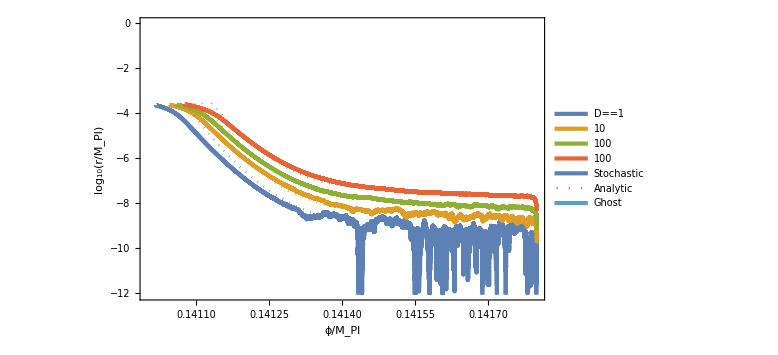

```mathematica
Show[ListPlot[{phivschi1,phivschi10,phivschi100,phivschi1000,{{ϕc,-30}},{{ϕc,-30}},{{ϕc,-30}}},FrameLabel->{"ϕ/M_Pl","log_10(r/M_Pl)"},PlotLegends->Placed[LineLegend[{D==1,10,100,100,"Stochastic","Analytic","Ghost"},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.8}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
ParametricPlot[{ϕc E^ξk[NN,1],Log10[ψk[NN,1]]},{NN,0,N1[1]+N2[1]},PlotStyle->{Dotted}],
ParametricPlot[{ϕc E^ξk[NN,10],Log10[ψk[NN,10]]},{NN,0,N1[10]+N2[10]},PlotStyle->{Color[2],Dotted}],
ParametricPlot[{ϕc E^ξk[NN,100],Log10[ψk[NN,100]]},{NN,0,N1[100]+N2[100]},PlotStyle->{Color[3],Dotted}],
ParametricPlot[{ϕc E^ξk[NN,1000],Log10[ψk[NN,1000]]},{NN,0,N1[1000]+N2[1000]},PlotStyle->{Color[4],Dotted}]]
```

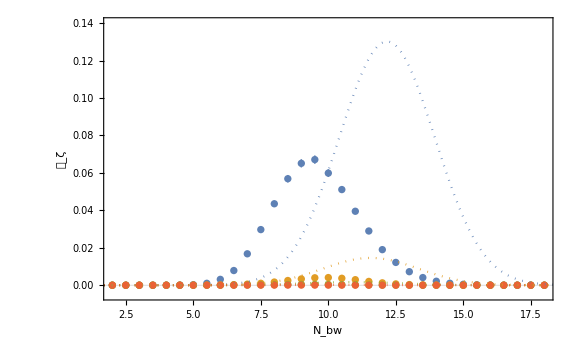

```mathematica
Show[ListPlot[{meancalP1,meancalP10,meancalP100,meancalP1000},FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->{{2,18},{-0.005,0.14}},GridLines->{None,{0}},Joined->False,IntervalMarkers->"Fences"],
Plot[{calPCG[NN,1],calPCG[NN,10],calPCG[NN,100],calPCG[NN,1000]},{NN,0,28},PlotStyle->{Dotted},PlotRange->Full]]
```

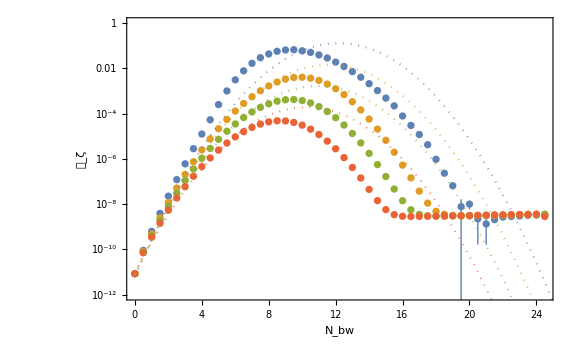

```mathematica
Show[ListLogPlot[{meancalP1,meancalP10,meancalP100,meancalP1000},FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{"D = 1",10,100,1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.38,0.2}]],LogPlot[{calPCG[NN,1],calPCG[NN,10],calPCG[NN,100],calPCG[NN,1000],0},{NN,0,28},PlotStyle->{Dotted,Dotted,Dotted,Dotted,{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{None,"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.38,0.2}]]]
```

## Param. Search

### Pi2 = 50

```mathematica
Π2=50;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

25000 √2

(63 π^2)/3125000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{6.40208,81.2255,80.9519,80.6744}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(1000000000 √10)

Log[(100000 √(10/21))/(√Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.72064

```mathematica
(*ξin1[Ht_]=-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc);
χin1[Ht_]=4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3;
Ht1[Dw_]=(M Sqrt[μ1 ϕc])/2 Sqrt[χ2[Dw]]-(μ1 ϕc M^2)/(12 μ2^2)χ2[Dw];
ξ2[Dw_]=-M/(2Sqrt[μ1 ϕc])Sqrt[χ2[Dw]]+M^2/(6 μ2^2)χ2[Dw];
χξ[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];*)
```

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;(*-M/(2Sqrt[μ1 ϕc])Sqrt[χ2[Dw]]+M^2/(6 μ2^2)χ2[Dw];*)
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
(*χξ[ξ_,Dw_]=(4μ1 ϕc)/M^2 ξ^2 UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]]);*)
```

107/200 (-107+√(11449-2000000 ξ))

1/400 (-22898+107^(1/3) Re[(1225043 (1+ⅈ √3))/((131079601-750000 Log[(100000 √(10/21))/(√Dw π^(1/4))]+500 √6 √(Log[(100000 √(10/21))/(√Dw π^(1/4))] (-131079601+375000 Log[(100000 √(10/21))/(√Dw π^(1/4))])))^(1/3))+107^(1/3) (1-ⅈ √3) (131079601-750000 Log[(100000 √(10/21))/(√Dw π^(1/4))]+500 √6 √(Log[(100000 √(10/21))/(√Dw π^(1/4))] (-131079601+375000 Log[(100000 √(10/21))/(√Dw π^(1/4))])))^(1/3)])

```mathematica
ξend=-M^2/8;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.00247925

-0.00125

```mathematica
Sqrt[χ2[1]]//N
```

3.29481

```mathematica
ϕc Exp[ξend]//N
```

0.141245

```mathematica
N1[Dw_]=Ht1[Dw];(*(Sqrt[χ2[Dw]]M ϕc^(1/2)μ1^(1/2))/2-(M^2 μ1 ϕc)/(12 μ2^2)χ2[Dw]*)
N2[Dw_,c_]=((M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2[Dw]])-(M^2 μ1 ϕc)/(12 μ2^2))c
```

c (-1250/34347+5/(2 √2 √Log[(100000 √(10/21))/(√Dw π^(1/4))]))

```mathematica
calPCG[NN_,Dw_,c_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2[Dw] ψ0[Dw]^2)Exp[-2χ2[Dw]((NN-N1[Dw]-N2[Dw,c])^2+2/(3 μ2^2)(N1[Dw]+N2[Dw,c]-NN)^3)/N1[Dw]^2];
```

```mathematica
phimin=0.1408;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {251/(1250 √2),Log[(√21 π^(1/4))/(10000000000 √10)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{37.6442,110.867,110.182,109.355}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨OverHat[𝒩]⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,10ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {251/(1250 √2),Log[(√21 π^(1/4))/(10000000000 √10)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ(𝒩̂)^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,10ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {251/(1250 √2),Log[(√21 π^(1/4))/(10000000000 √10)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000,"Stochastic","Analytic"(*,"Ghost"*)},LegendLayout->{"Row",3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.3,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,10ξend,0},PlotStyle->{Dotted,Color[1]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[2]]]Exp[χξ[ξ,DwList[[2]]]]/M]},{ξ,10ξend,0},PlotStyle->{Dotted,Color[2]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[3]]]Exp[χξ[ξ,DwList[[3]]]]/M]},{ξ,10ξend,0},PlotStyle->{Dotted,Color[3]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[4]]]Exp[χξ[ξ,DwList[[4]]]]/M]},{ξ,10ξend,0},PlotStyle->{Dotted,Color[4]}]];
```

```mathematica
Export["samples_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

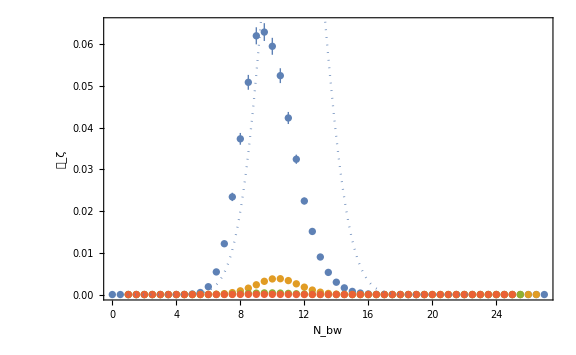

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Plot[calPCG[NN,1,0],{NN,0,2(N1[1]+N2[1,0])},PlotStyle->{Dotted},PlotRange->Full]]
```

```mathematica
FigcalPshifted=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.4,0.2}]],
LogPlot[calPCG[NN,DwList[[1]],0.5],{NN,0,2(N1[DwList[[1]]]+N2[DwList[[1]],0.5])},PlotStyle->{Dotted,Color[1]}],LogPlot[calPCG[NN,DwList[[2]],1.5],{NN,0,2(N1[DwList[[2]]]+N2[DwList[[2]],1.5])},PlotStyle->{Dotted,Color[2]}],LogPlot[calPCG[NN,DwList[[3]],1.5],{NN,0,2(N1[DwList[[3]]]+N2[DwList[[3]],1.5])},PlotStyle->{Dotted,Color[3]}],LogPlot[calPCG[NN,DwList[[4]],1.5],{NN,0,2(N1[DwList[[4]]]+N2[DwList[[4]],1.5])},PlotStyle->{Dotted,Color[4]}],LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.4,0.2}]]];
```

```mathematica
Export["calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x]//Simplify;
Vy[x_,y_]=D[V[x,y], y]//Simplify;
```

```mathematica
clsol=NDSolve[{x'[NN]==-Vx[x[NN],y[NN]]/V[x[NN],y[NN]]UnitStep[Log[x[NN]/ϕc]-ξend],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]] UnitStep[Log[x[NN]/ϕc]-ξend],x[0]==ϕc,y[0]==ψ0[1]},{x[NN],y[NN]},{NN,0,N1[1]+N2[1]},WorkingPrecision->30][[1]];
```

```mathematica
phicl[NN_]=x[NN]/.clsol;
psicl[NN_]=y[NN]/.clsol;
```

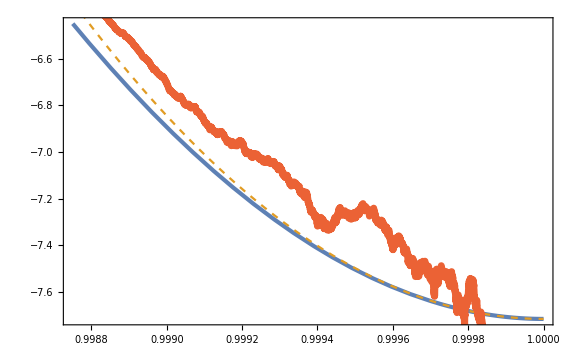

```mathematica
Show[ParametricPlot[{phicl[NN]/ϕc,Log10[psicl[NN]/M]},{NN,0,N1[1]+N2[1]},PlotRange->Full],ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotRange->Full,PlotStyle->{Color[2],Dashed}],ListPlot[phivschi[[1]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

```mathematica
Exp[3.04] 10^10//N
```

2.09052×10^11

### Pi2 = 100

```mathematica
Π2=100;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

50000 √2

(63 π^2)/12500000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=4;
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{8.44571,8.4795,8.50195,8.52375}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/2)^(1/4))/(2000000000 √5)

Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))]

```mathematica
χ2[1]//N
```

11.0291

```mathematica
ξ2[Dw_]=-M/(2Sqrt[μ1 ϕc])Sqrt[χ2[Dw]];
χξ[ξ_,Dw_]=(4μ1 ϕc)/M^2 ξ^2 UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]]);
```

```mathematica
ξend=-M^2/8;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.0016605

-0.00125

```mathematica
ϕc Exp[ξend]//N
```

0.141245

```mathematica
N1[Dw_]=(Sqrt[χ2[Dw]]M ϕc^(1/2)μ1^(1/2))/2
N2[Dw_]=(M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2[Dw]])
```

5 √Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))]

5/(2 √Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])

```mathematica
calPCG[NN_,Dw_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2[Dw] ψ0[Dw]^2)Exp[-2χ2[Dw](NN-N1[Dw]-N2[Dw])^2/N1[Dw]^2];
```

```mathematica
phimin=0.1409;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {501/(2500 √2),Log[(√(21/5) (π/2)^(1/4))/20000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{41.629,40.5213,39.6866,38.8186}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {501/(2500 √2),Log[(√(21/5) (π/2)^(1/4))/20000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {501/(2500 √2),Log[(√(21/5) (π/2)^(1/4))/20000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, water]==1,10,100,100,"Stochastic","Analytic","Ghost"},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.85}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[1]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[2]]]Exp[χξ[ξ,DwList[[2]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[2]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[3]]]Exp[χξ[ξ,DwList[[3]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[3]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[4]]]Exp[χξ[ξ,DwList[[4]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[4]}]];
```

```mathematica
Export["samples_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

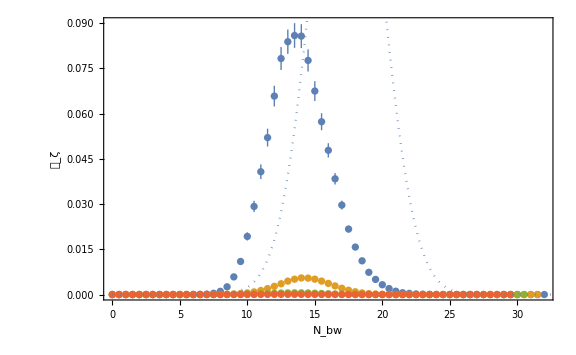

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Plot[calPCG[NN,1],{NN,0,2(N1[1]+N2[1])},PlotStyle->{Dotted},PlotRange->Full]]
```

Part::pkspec1: The expression Dwi cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value 2 (5/(2 √Log[(100000 √(5/21) 2^(3/4))/(π^(1/4) √Part[«2»])])+5 √Log[(100000 √(5/21) 2^(3/4))/(π^(1/4) √Part[«2»])]) in {NN,0,2 (5/(2 √Log[100000 Power[«2»] Power[«2»] Power[«2»] Power[«2»]])+5 √Log[100000 Power[«2»] Power[«2»] Power[«2»] Power[«2»]])} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

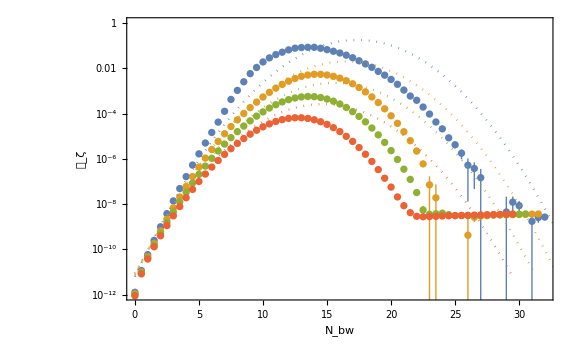

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, water]==1,10,100,1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.38,0.2}]],LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->1},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->2},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->3},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->4},LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.38,0.2}]]]
```

```mathematica
Export["calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x]//Simplify;
Vy[x_,y_]=D[V[x,y], y]//Simplify;
```

```mathematica
clsol=NDSolve[{x'[NN]==-Vx[x[NN],y[NN]]/V[x[NN],y[NN]]UnitStep[Log[x[NN]/ϕc]-ξend],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]] UnitStep[Log[x[NN]/ϕc]-ξend],x[0]==ϕc,y[0]==ψ0[1]},{x[NN],y[NN]},{NN,0,N1[1]+N2[1]},WorkingPrecision->30][[1]];
```

```mathematica
phicl[NN_]=x[NN]/.clsol;
psicl[NN_]=y[NN]/.clsol;
```

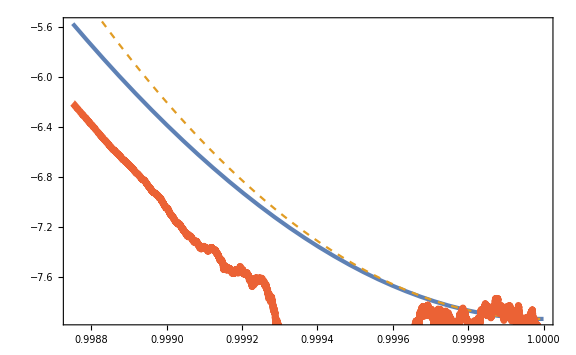

```mathematica
Show[ParametricPlot[{phicl[NN]/ϕc,Log10[psicl[NN]/M]},{NN,0,N1[1]+N2[1]},PlotRange->Full],ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotRange->Full,PlotStyle->{Color[2],Dashed}],ListPlot[phivschi[[1]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

### Pi2 = 150

```mathematica
Π2=150;
As=21 10^-10;
M=1/10;
μ1=3 10^5;
ϕc=Π2/(M^2 μ1)
μ2=10(*107/10*);
Λ4=12 π^2 As/μ1^2
```

1/20

(7 π^2)/25000000000000000000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√7 √Dw (π/3)^(1/4))/(4000000000 √5)

Log[(100000 √10)/(3^(1/4) √7 √Dw π^(1/4))]

```mathematica
χ2[1]//N
```

11.1304

```mathematica
ξ2[Dw_]=-M/(2Sqrt[μ1 ϕc])Sqrt[χ2[Dw]];
χξ[ξ_,Dw_]=(4μ1 ϕc)/M^2 ξ^2 UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]]);
```

```mathematica
ξend=-M^2/8;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.00136201

-0.00125

```mathematica
ϕc Exp[ξend]//N
```

0.141245

```mathematica
N1[Dw_]=(Sqrt[χ2[Dw]]M ϕc^(1/2)μ1^(1/2))/2
N2[Dw_]=(M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2[Dw]])
```

5 √Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))]

5/(2 √Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])

```mathematica
calPCG[NN_,Dw_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2[Dw] ψ0[Dw]^2)Exp[-2χ2[Dw](NN-N1[Dw]-N2[Dw])^2/N1[Dw]^2];
```

```mathematica
phimin=0.1409;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {501/(2500 √2),Log[(√(21/5) (π/2)^(1/4))/20000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{41.629,40.5213,39.6866,38.8186}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {501/(2500 √2),Log[(√(21/5) (π/2)^(1/4))/20000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {501/(2500 √2),Log[(√(21/5) (π/2)^(1/4))/20000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, water]==1,10,100,100,"Stochastic","Analytic","Ghost"},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.85}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[1]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[2]]]Exp[χξ[ξ,DwList[[2]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[2]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[3]]]Exp[χξ[ξ,DwList[[3]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[3]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[4]]]Exp[χξ[ξ,DwList[[4]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[4]}]];
```

```mathematica
Export["samples_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Plot[calPCG[NN,1],{NN,0,2(N1[1]+N2[1])},PlotStyle->{Dotted},PlotRange->Full]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, water]==1,10,100,1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.38,0.2}]],LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->1},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->2},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->3},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->4},LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.38,0.2}]]]
```

Part::pkspec1: The expression Dwi cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value 2 (5/(2 √Log[(100000 √(5/21) 2^(3/4))/(π^(1/4) √Part[«2»])])+5 √Log[(100000 √(5/21) 2^(3/4))/(π^(1/4) √Part[«2»])]) in {NN,0,2 (5/(2 √Log[100000 Power[«2»] Power[«2»] Power[«2»] Power[«2»]])+5 √Log[100000 Power[«2»] Power[«2»] Power[«2»] Power[«2»]])} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

-Graphics-

```mathematica
Export["calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x]//Simplify;
Vy[x_,y_]=D[V[x,y], y]//Simplify;
```

```mathematica
clsol=NDSolve[{x'[NN]==-Vx[x[NN],y[NN]]/V[x[NN],y[NN]]UnitStep[Log[x[NN]/ϕc]-ξend],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]] UnitStep[Log[x[NN]/ϕc]-ξend],x[0]==ϕc,y[0]==ψ0[1]},{x[NN],y[NN]},{NN,0,N1[1]+N2[1]},WorkingPrecision->30][[1]];
```

```mathematica
phicl[NN_]=x[NN]/.clsol;
psicl[NN_]=y[NN]/.clsol;
```

```mathematica
Show[ParametricPlot[{phicl[NN]/ϕc,Log10[psicl[NN]/M]},{NN,0,N1[1]+N2[1]},PlotRange->Full],ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotRange->Full,PlotStyle->{Color[2],Dashed}],ListPlot[phivschi[[1]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

### Pi2 = 200

```mathematica
Π2=200;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

100000 √2

(63 π^2)/50000000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=4;
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data_2807/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data_2807/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data_2807/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{10.1393,10.3702,10.515,10.6179}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(4000000000 √5)

Log[(200000 √(5/21))/(√Dw π^(1/4))]

```mathematica
χ2[1]//N
```

11.2023

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
```

107/200 (-107+√(11449-8000000 ξ))

```mathematica
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
```

1/400 (-22898+107^(1/3) Re[(1225043 (1+ⅈ √3))/((131079601-3000000 Log[(200000 √(5/21))/(√Dw π^(1/4))]+1000 √6 √(Log[(200000 √(5/21))/(√Dw π^(1/4))] (-131079601+1500000 Log[(200000 √(5/21))/(√Dw π^(1/4))])))^(1/3))+107^(1/3) (1-ⅈ √3) (131079601-3000000 Log[(200000 √(5/21))/(√Dw π^(1/4))]+1000 √6 √(Log[(200000 √(5/21))/(√Dw π^(1/4))] (-131079601+1500000 Log[(200000 √(5/21))/(√Dw π^(1/4))])))^(1/3)])

```mathematica
Ht1[1]//N
```

22.2672

```mathematica
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;(*-M/(2Sqrt[μ1 ϕc])Sqrt[χ2[Dw]]+M^2/(6 μ2^2)χ2[Dw];*)
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
(*χξ[ξ_,Dw_]=(4μ1 ϕc)/M^2 ξ^2 UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]]);*)
```

```mathematica
ξ2[1]//N
```

-0.0013299

```mathematica
ξend=-M^2/8;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.0013299

-0.00125

```mathematica
ϕc Exp[ξend]//N
```

0.141245

```mathematica
N1[Dw_]=Ht1[Dw];(*(Sqrt[χ2[Dw]]M ϕc^(1/2)μ1^(1/2))/2-(M^2 μ1 ϕc)/(12 μ2^2)χ2[Dw]*)
N2[Dw_]=(M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2[Dw]])-(M^2 μ1 ϕc)/(12 μ2^2)
```

-5000/34347+5/(√2 √Log[(200000 √(5/21))/(√Dw π^(1/4))])

```mathematica
calPCG[NN_,Dw_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2[Dw] ψ0[Dw]^2)Exp[-2χ2[Dw]((NN-N1[Dw]-N2[Dw])^2+2/(3 μ2^2)(N1[Dw]+N2[Dw]-NN)^3)/N1[Dw]^2];
```

```mathematica
phimin=0.1412;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {1001/(5000 √2),Log[(√21 π^(1/4))/(40000000000 √5)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{47.5808,46.2284,45.1964,44.0866}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {1001/(5000 √2),Log[(√21 π^(1/4))/(40000000000 √5)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {1001/(5000 √2),Log[(√21 π^(1/4))/(40000000000 √5)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

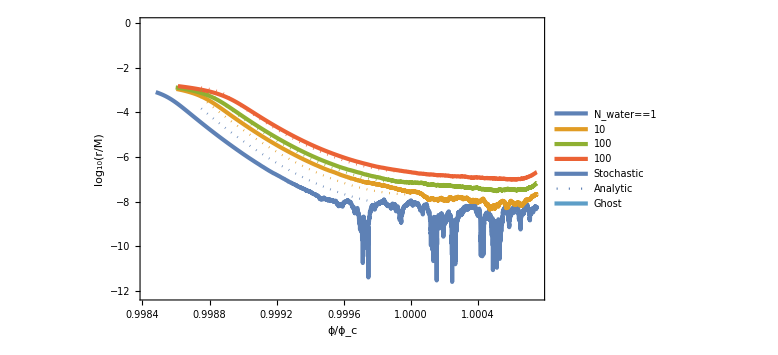

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, water]==1,10,100,100,"Stochastic","Analytic","Ghost"},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.85}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[1]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[2]]]Exp[χξ[ξ,DwList[[2]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[2]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[3]]]Exp[χξ[ξ,DwList[[3]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[3]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[4]]]Exp[χξ[ξ,DwList[[4]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[4]}]]
```

```mathematica
Export["samples_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

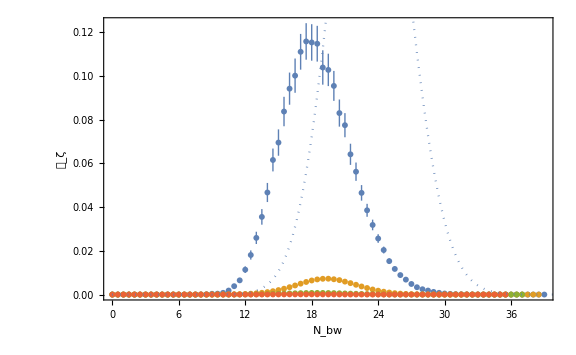

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Plot[calPCG[NN,1],{NN,0,2(N1[1]+N2[1])},PlotStyle->{Dotted},PlotRange->Full]]
```

Part::pkspec1: The expression Dwi cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value 2 (-5000/34347+5/(√2 √Log[(200000 √(5/21))/(π^(1/4) √Part[«2»])])+1/400 (-22898+107^(1/3) Re[Times[«3»]+Times[«3»]])) in {NN,0,2 (-5000/34347+5/(√2 √Log[200000 Power[«2»] Power[«2»] Power[«2»]])+1/400 (-22898+107^(1/3) Re[Plus[«2»]]))} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

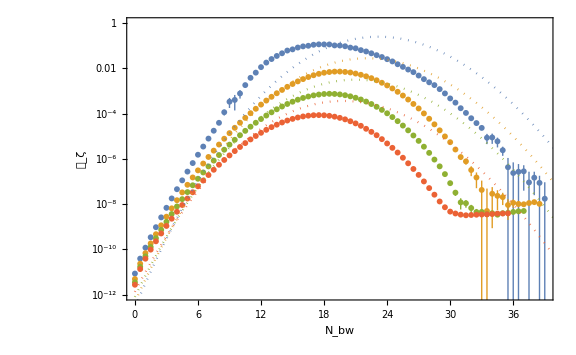

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, water]==1,10,100,1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.4,0.2}]],LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->1},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->2},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->3},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->4},LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.4,0.2}]]]
```

```mathematica
Export["calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x]//Simplify;
Vy[x_,y_]=D[V[x,y], y]//Simplify;
```

```mathematica
clsol=NDSolve[{x'[NN]==-Vx[x[NN],y[NN]]/V[x[NN],y[NN]]UnitStep[Log[x[NN]/ϕc]-ξend],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]] UnitStep[Log[x[NN]/ϕc]-ξend],x[0]==ϕc,y[0]==ψ0[1]},{x[NN],y[NN]},{NN,0,N1[1]+N2[1]},WorkingPrecision->30][[1]];
```

```mathematica
phicl[NN_]=x[NN]/.clsol;
psicl[NN_]=y[NN]/.clsol;
```

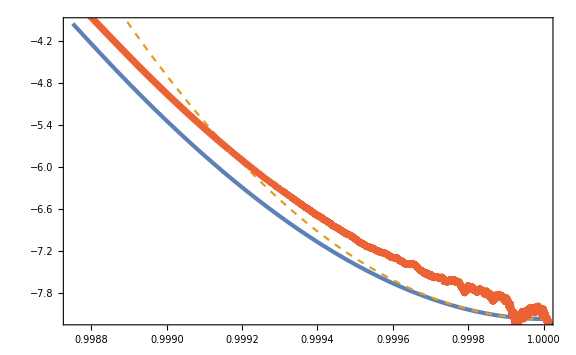

```mathematica
Show[ParametricPlot[{phicl[NN]/ϕc,Log10[psicl[NN]/M]},{NN,0,N1[1]+N2[1]},PlotRange->Full],ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotRange->Full,PlotStyle->{Color[2],Dashed}],ListPlot[phivschi[[1]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

### Pi2 = 500

```mathematica
Π2=500;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

250000 √2

(63 π^2)/312500000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=4;
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{15.4235,15.4441,15.463,15.4808}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/10)^(1/4))/10000000000

Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
χ2[1]//N
```

11.4314

```mathematica
ξ2[Dw_]=-M/(2Sqrt[μ1 ϕc])Sqrt[χ2[Dw]];
χξ[ξ_,Dw_]=(4μ1 ϕc)/M^2 ξ^2 UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]]);
```

```mathematica
ξend=-M^2/8;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.000756023

-0.00125

```mathematica
ϕc Exp[ξend]//N
```

0.141245

```mathematica
N1[Dw_]=(Sqrt[χ2[Dw]]M ϕc^(1/2)μ1^(1/2))/2
N2[Dw_]=(M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2[Dw]])
```

5 √5 √Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))]

(5 √5)/(2 √Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))])

```mathematica
calPCG[NN_,Dw_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2[Dw] ψ0[Dw]^2)Exp[-2χ2[Dw](NN-N1[Dw]-N2[Dw])^2/N1[Dw]^2];
```

```mathematica
phimin=0.1412;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {2501/(12500 √2),Log[(√21 (π/10)^(1/4))/100000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{61.2393,59.0481,57.3973,55.677}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {2501/(12500 √2),Log[(√21 (π/10)^(1/4))/100000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {2501/(12500 √2),Log[(√21 (π/10)^(1/4))/100000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, water]==1,10,100,100,"Stochastic","Analytic","Ghost"},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.4,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[1]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[2]]]Exp[χξ[ξ,DwList[[2]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[2]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[3]]]Exp[χξ[ξ,DwList[[3]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[3]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[4]]]Exp[χξ[ξ,DwList[[4]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[4]}]];
```

```mathematica
Export["samples_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

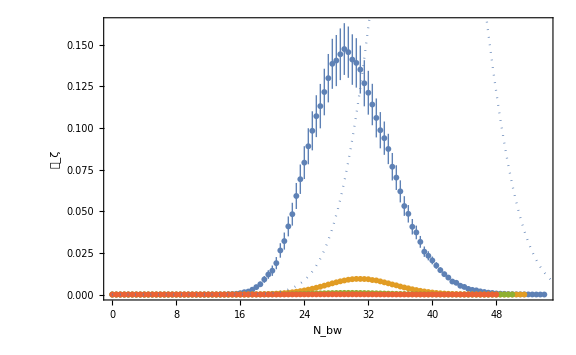

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Plot[calPCG[NN,1],{NN,0,2(N1[1]+N2[1])},PlotStyle->{Dotted},PlotRange->Full]]
```

Part::pkspec1: The expression Dwi cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value 2 ((5 √5)/(2 √Log[(100000 10^(3/4))/(√21 π^(1/4) √Part[«2»])])+5 √5 √Log[(100000 10^(3/4))/(√21 π^(1/4) √Part[«2»])]) in {NN,0,2 ((5 √5)/(2 √Log[100000 Power[«2»] Power[«2»] Power[«2»] Power[«2»]])+5 √5 √Log[100000 Power[«2»] Power[«2»] Power[«2»] Power[«2»]])} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

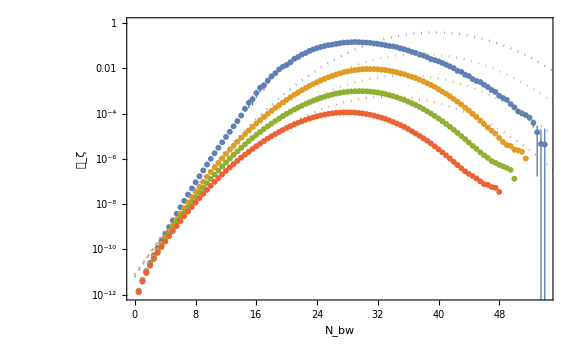

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, water]==1,10,100,1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.5,0.2}]],LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->1},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->2},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->3},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->4},LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.5,0.2}]]]
```

```mathematica
Export["calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x]//Simplify;
Vy[x_,y_]=D[V[x,y], y]//Simplify;
```

```mathematica
clsol=NDSolve[{x'[NN]==-Vx[x[NN],y[NN]]/V[x[NN],y[NN]]UnitStep[Log[x[NN]/ϕc]-ξend],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]] UnitStep[Log[x[NN]/ϕc]-ξend],x[0]==ϕc,y[0]==ψ0[1]},{x[NN],y[NN]},{NN,0,N1[1]+N2[1]},WorkingPrecision->30][[1]];
```

```mathematica
phicl[NN_]=x[NN]/.clsol;
psicl[NN_]=y[NN]/.clsol;
```

```mathematica
Show[ParametricPlot[{phicl[NN]/ϕc,Log10[psicl[NN]/M]},{NN,0,N1[1]+N2[1]},PlotRange->Full],ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotRange->Full,PlotStyle->{Color[2],Dashed}],ListPlot[phivschi[[1]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

### Pi2 = 1000

```mathematica
Π2=1000;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

500000 √2

(63 π^2)/1250000000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=4;
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{19.5878,19.5956,19.6031,19.6104}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/20000000000

Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
χ2[1]//N
```

11.6047

```mathematica
ξ2[Dw_]=-M/(2Sqrt[μ1 ϕc])Sqrt[χ2[Dw]];
χξ[ξ_,Dw_]=(4μ1 ϕc)/M^2 ξ^2 UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]]);
```

```mathematica
ξend=-M^2/8;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.000538626

-0.00125

```mathematica
ϕc Exp[ξend]//N
```

0.141245

```mathematica
N1[Dw_]=(Sqrt[χ2[Dw]]M ϕc^(1/2)μ1^(1/2))/2
N2[Dw_]=(M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2[Dw]])
```

5 √10 √Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))]

(5 √(5/2))/(√Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))])

```mathematica
calPCG[NN_,Dw_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2[Dw] ψ0[Dw]^2)Exp[-2χ2[Dw](NN-N1[Dw]-N2[Dw])^2/N1[Dw]^2];
```

```mathematica
phimin=0.1412;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {5001/(25000 √2),Log[(√21 (π/5)^(1/4))/200000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{75.0441,72.2145,70.0714,67.8342}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {5001/(25000 √2),Log[(√21 (π/5)^(1/4))/200000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {5001/(25000 √2),Log[(√21 (π/5)^(1/4))/200000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, water]==1,10,100,100,"Stochastic","Analytic","Ghost"},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.4,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[1]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[2]]]Exp[χξ[ξ,DwList[[2]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[2]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[3]]]Exp[χξ[ξ,DwList[[3]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[3]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[4]]]Exp[χξ[ξ,DwList[[4]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[4]}]];
```

```mathematica
Export["samples_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

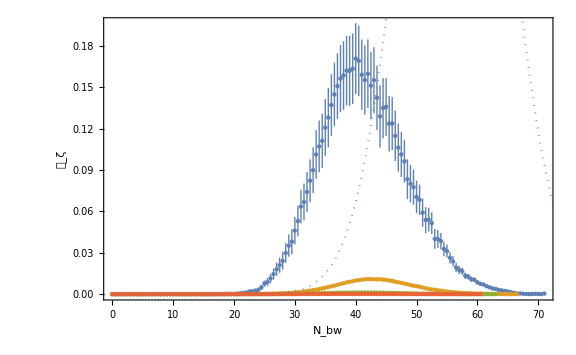

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Plot[calPCG[NN,1],{NN,0,2(N1[1]+N2[1])},PlotStyle->{Dotted},PlotRange->Full]]
```

Part::pkspec1: The expression Dwi cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value 2 ((5 √(5/2))/(√Log[(200000 5^(3/4))/(√21 π^(1/4) √Part[«2»])])+5 √10 √Log[(200000 5^(3/4))/(√21 π^(1/4) √Part[«2»])]) in {NN,0,2 ((5 √(5/2))/(√Log[200000 Power[«2»] Power[«2»] Power[«2»] Power[«2»]])+5 √10 √Log[200000 Power[«2»] Power[«2»] Power[«2»] Power[«2»]])} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

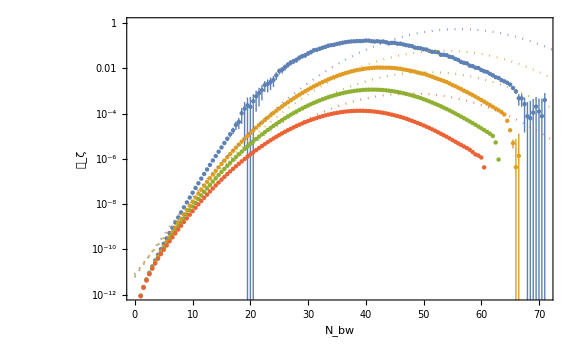

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, water]==1,10,100,1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->1},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->2},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->3},LogPlot[calPCG[NN,DwList[[Dwi]]],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]]])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->4},LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.6,0.2}]]]
```

```mathematica
Export["calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x]//Simplify;
Vy[x_,y_]=D[V[x,y], y]//Simplify;
```

```mathematica
clsol=NDSolve[{x'[NN]==-Vx[x[NN],y[NN]]/V[x[NN],y[NN]]UnitStep[Log[x[NN]/ϕc]-ξend],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]] UnitStep[Log[x[NN]/ϕc]-ξend],x[0]==ϕc,y[0]==ψ0[1]},{x[NN],y[NN]},{NN,0,N1[1]+N2[1]},WorkingPrecision->30][[1]];
```

```mathematica
phicl[NN_]=x[NN]/.clsol;
psicl[NN_]=y[NN]/.clsol;
```

```mathematica
Show[ParametricPlot[{phicl[NN]/ϕc,Log10[psicl[NN]/M]},{NN,0,N1[1]+N2[1]},PlotRange->Full],ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotRange->Full,PlotStyle->{Color[2],Dashed}],ListPlot[phivschi[[1]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

### Pi2 = 2000

```mathematica
Π2=2000;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

1000000 √2

(63 π^2)/5000000000000000000000

```mathematica
1/μ1//N
1/μ2^2//N
```

7.07107×10^-7

0.00873439

```mathematica
DwList={1(*,10,100,1000*)};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{22.8576}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/(20000000000 2^(3/4))

Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)]

```mathematica
χ2[1]//N
```

11.778

```mathematica
(*ξin1[Ht_]=-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc);
χin1[Ht_]=4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3;
Ht1[Dw_]=(M Sqrt[μ1 ϕc])/2 Sqrt[χ2[Dw]]-(μ1 ϕc M^2)/(12 μ2^2)χ2[Dw];
ξ2[Dw_]=-M/(2Sqrt[μ1 ϕc])Sqrt[χ2[Dw]]+M^2/(6 μ2^2)χ2[Dw];
χξ[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];*)
```

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;(*-M/(2Sqrt[μ1 ϕc])Sqrt[χ2[Dw]]+M^2/(6 μ2^2)χ2[Dw];*)
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
(*χξ[ξ_,Dw_]=(4μ1 ϕc)/M^2 ξ^2 UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]]);*)
```

107/200 (-107+√(11449-80000000 ξ))

1/400 (-22898+107^(1/3) Re[(1225043 (1+ⅈ √3))/(131079601-7500000 (-2 Log[21]+4 Log[200000]-2 Log[Dw]+Log[250/π])+2000 √15 √(Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)] (-131079601+3750000 (-2 Log[21]+4 Log[200000]-2 Log[Dw]+Log[250/π]))))^(1/3)+107^(1/3) (1-ⅈ √3) (131079601-7500000 (-2 Log[21]+4 Log[200000]-2 Log[Dw]+Log[250/π])+2000 √15 √(Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)] (-131079601+3750000 (-2 Log[21]+4 Log[200000]-2 Log[Dw]+Log[250/π]))))^(1/3)])

```mathematica
Ht1[1]//N
ξ2[1]//N
```

65.3173

-0.000512906

```mathematica
ξend=-M^2/8;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.000512906

-0.00125

```mathematica
ϕc Exp[ξend]//N
```

0.141245

```mathematica
N1[Dw_]=Ht1[Dw];(*(Sqrt[χ2[Dw]]M ϕc^(1/2)μ1^(1/2))/2-(M^2 μ1 ϕc)/(12 μ2^2)χ2[Dw]*)
N2[Dw_,c_]=((M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2[Dw]])-(M^2 μ1 ϕc)/(12 μ2^2))c
```

c (-50000/34347+(5 √5)/(√Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)]))

```mathematica
calPCG[NN_,Dw_,c_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2[Dw] ψ0[Dw]^2)Exp[-2χ2[Dw]((NN-N1[Dw]-N2[Dw,c])^2+2/(3 μ2^2)(N1[Dw]+N2[Dw,c]-NN)^3)/N1[Dw]^2];
```

```mathematica
phimin=0.1412;
phimax=ϕc+15/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {40003/(200000 √2),Log[(√21 (π/5)^(1/4))/(200000000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

{83.4406}

```mathematica
f1int[1.00005ϕc,logrmin[DwList[[1]]]][[1]]
```

InterpolatingFunction::dmval: Input value {0.141428,Log[(√21 (π/5)^(1/4))/(200000000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

76.8771

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩̂⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {40003/(200000 √2),Log[(√21 (π/5)^(1/4))/(200000000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-Graphics-}

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ(𝒩̂)^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {40003/(200000 √2),Log[(√21 (π/5)^(1/4))/(200000000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-Graphics-}

```mathematica
Do[Export["N_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

Part::partw: Part 2 of {1} does not exist.

Part::partw: Part 2 of {1.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

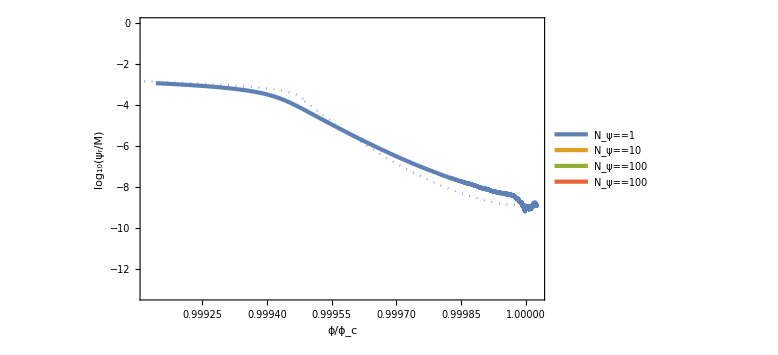

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==100,"Stochastic","Analytic"(*,"Ghost"*)},LegendLayout->{"Row",3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.4,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[1]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[2]]]Exp[χξ[ξ,DwList[[2]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[2]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[3]]]Exp[χξ[ξ,DwList[[3]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[3]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[4]]]Exp[χξ[ξ,DwList[[4]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[4]}]]
```

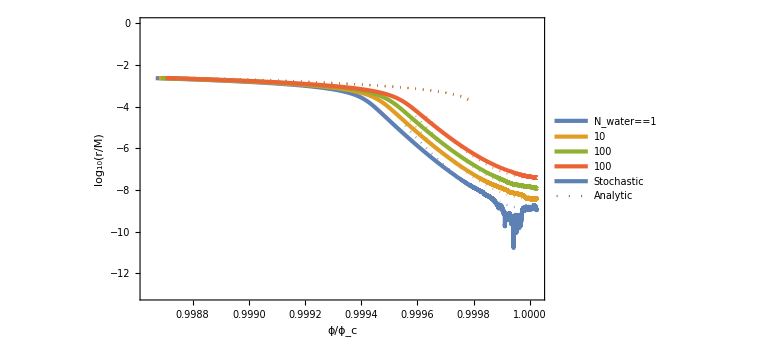

```mathematica
(*SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, water]==1,10,100,100,"Stochastic","Analytic"(*,"Ghost"*)},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.4,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,ξ2[DwList[[1]]]},PlotStyle->{Dotted,Color[1]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[2]]]Exp[χξ[ξ,DwList[[2]]]]/M]},{ξ,ξend,ξ2[DwList[[1]]]},PlotStyle->{Dotted,Color[2]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[3]]]Exp[χξ[ξ,DwList[[3]]]]/M]},{ξ,ξend,ξ2[DwList[[1]]]},PlotStyle->{Dotted,Color[3]}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[4]]]Exp[χξ[ξ,DwList[[4]]]]/M]},{ξ,ξend,ξ2[DwList[[1]]]},PlotStyle->{Dotted,Color[4]}],
ParametricPlot[{E^ξin1[Ht],Log10[ψ0[DwList[[1]]]Exp[χin1[Ht]]/M]},{Ht,0,Ht1[DwList[[1]]]},PlotStyle->{Dotted,Color[1]}],
ParametricPlot[{E^ξin1[Ht],Log10[ψ0[DwList[[2]]]Exp[χin1[Ht]]/M]},{Ht,0,Ht1[DwList[[2]]]},PlotStyle->{Dotted,Color[2]}],
ParametricPlot[{E^ξin1[Ht],Log10[ψ0[DwList[[3]]]Exp[χin1[Ht]]/M]},{Ht,0,Ht1[DwList[[3]]]},PlotStyle->{Dotted,Color[3]}],
ParametricPlot[{E^ξin1[Ht],Log10[ψ0[DwList[[4]]]Exp[χin1[Ht]]/M]},{Ht,0,Ht1[DwList[[4]]]},PlotStyle->{Dotted,Color[4]}]]*)
```

```mathematica
Export["samples_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

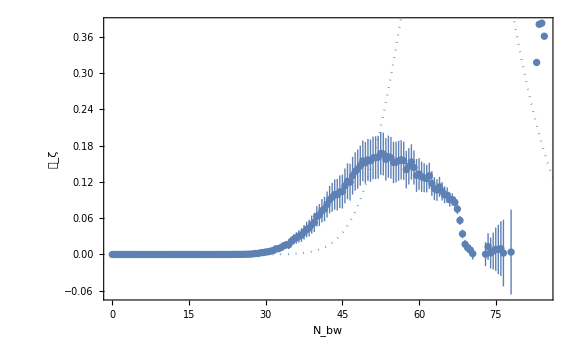

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Plot[calPCG[NN,1,1],{NN,0,2(N1[1]+N2[1,1])},PlotStyle->{Dotted},PlotRange->Full]]
```

Part::pkspec1: The expression Dwi cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value 2 (-50000/34347+(5 √5)/(√Log[(200000 5^(3/4) Times[«2»]^(1/4))/(√21 √Part[«2»])])+1/400 (-22898+107^(1/3) Re[Times[«3»]+Times[«3»]])) in {NN,0,2 (-50000/34347+(5 √5)/(√Log[200000 Power[«2»] Power[«2»] Power[«2»] Power[«2»]])+1/400 (-22898+107^(1/3) Re[Plus[«2»]]))} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

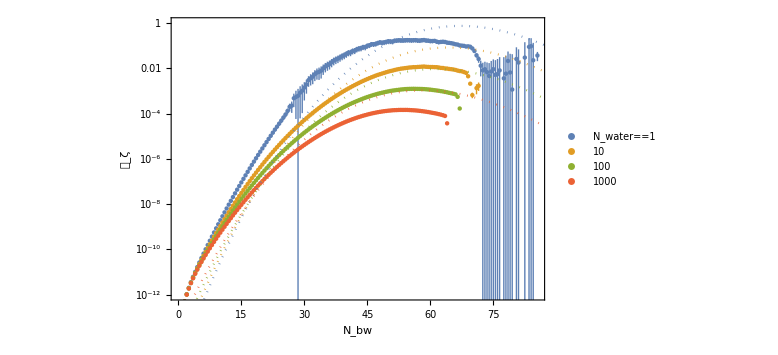

```mathematica
FigcalPc1=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, water]==1,10,100,1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[calPCG[NN,DwList[[Dwi]],1],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]],1])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->1},LogPlot[calPCG[NN,DwList[[Dwi]],1],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]],1])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->2},LogPlot[calPCG[NN,DwList[[Dwi]],1],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]],1])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->3},LogPlot[calPCG[NN,DwList[[Dwi]],1],{NN,0,2(N1[DwList[[Dwi]]]+N2[DwList[[Dwi]],1])},PlotStyle->{Dotted,Color[Dwi]}]/.{Dwi->4},LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}}(*,PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.6,0.2}]*)]]
```

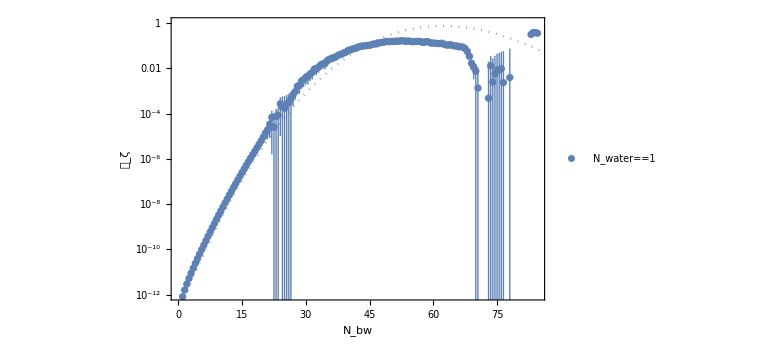

```mathematica
FigcalPshifted=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, water]==1,10,100,1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[calPCG[NN,DwList[[1]],-1.7],{NN,0,2(N1[DwList[[1]]]+N2[DwList[[1]],-1.7])},PlotStyle->{Dotted,Color[1]}](*,LogPlot[calPCG[NN,DwList[[2]],-1],{NN,0,2(N1[DwList[[2]]]+N2[DwList[[2]],-1])},PlotStyle->{Dotted,Color[2]}],LogPlot[calPCG[NN,DwList[[3]],-0.5],{NN,0,2(N1[DwList[[3]]]+N2[DwList[[3]],-0.5])},PlotStyle->{Dotted,Color[3]}],LogPlot[calPCG[NN,DwList[[4]],0],{NN,0,2(N1[DwList[[4]]]+N2[DwList[[4]],0])},PlotStyle->{Dotted,Color[4]}],LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}}(*,PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.6,0.2}]*)]*)]
```

```mathematica
Export["calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x]//Simplify;
Vy[x_,y_]=D[V[x,y], y]//Simplify;
```

```mathematica
clsol=NDSolve[{x'[NN]==-Vx[x[NN],y[NN]]/V[x[NN],y[NN]]UnitStep[Log[x[NN]/ϕc]-ξend],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]] UnitStep[Log[x[NN]/ϕc]-ξend],x[0]==ϕc,y[0]==ψ0[1]},{x[NN],y[NN]},{NN,0,N1[1]+N2[1]},WorkingPrecision->30][[1]];
```

```mathematica
phicl[NN_]=x[NN]/.clsol;
psicl[NN_]=y[NN]/.clsol;
```

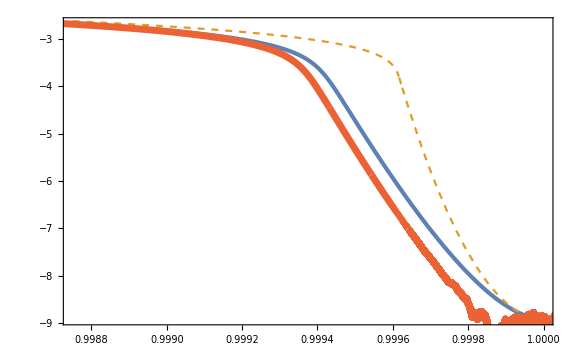

```mathematica
Show[ParametricPlot[{phicl[NN]/ϕc,Log10[psicl[NN]/M]},{NN,0,N1[1]+N2[1]},PlotRange->Full],ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotRange->Full,PlotStyle->{Color[2],Dashed}],ListPlot[phivschi[[1]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

#### D = 5

```mathematica
fndata5=Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D=5.dat"],#[[2]]>0&]];
trajdata5=Import["StocDeltaN/data/sample_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D=5.dat"];
calPdata5=Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D=5.dat"],#[[2]]>0&];
```

```mathematica
f1List5=Table[{fndata5[[i,1]],Log10[fndata5[[i,2]]],fndata5[[i,3]]-UnitStep[-fndata5[[i,3]]]},{i,1,Length[fndata5]}];
g2List5=Table[{fndata5[[i,1]],Log10[fndata5[[i,2]]],Log10[fndata5[[i,4]]]},{i,1,Length[fndata5]}];
phivschi5=Table[{trajdata5[[i,2]]/ϕc,Log10[Abs[trajdata5[[i,3]]]/M]},{i,Length[trajdata5]}];
Ndata5=Table[{trajdata5[[i,1]],trajdata5[[i,4]]},{i,Length[trajdata5]}];
dN2data5=Table[{trajdata5[[i,1]],trajdata5[[i,5]]},{i,Length[trajdata5]}];
meancalP5=Table[{calPdata5[[i,1]],calPdata5[[i,2]]±calPdata5[[i,3]]},{i,Length[calPdata5]}];
```

```mathematica
f1int5[ϕ_,logr_]=Interpolation[f1List5][ϕ,logr];
g2int5[ϕ_,logr_]=Interpolation[g2List5][ϕ,logr];
```

```mathematica
f1int5[ϕc,-5]
```

23.8594

```mathematica
Ncontour5=Show[ContourPlot[f1int5[ϕ ϕc,logr+Log10[M]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[5]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==5}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int5[phimax,logrmin[5]],5}]]],
ListPlot[phivschi5,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[5]Exp[χξ[ξ,5]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]]
```

InterpolatingFunction::dmval: Input value {40003/(200000 √2),Log[(√21 π^(1/4))/(40000000000 10^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
dN2contour5=Show[ContourPlot[g2int5[ϕ ϕc,logr+Log10[M]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[5]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==5}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int5[phimax,logrmin[5]]}]],ListPlot[phivschi5,PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[5]Exp[χξ[ξ,5]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]]
```

InterpolatingFunction::dmval: Input value {40003/(200000 √2),Log[(√21 π^(1/4))/(40000000000 10^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

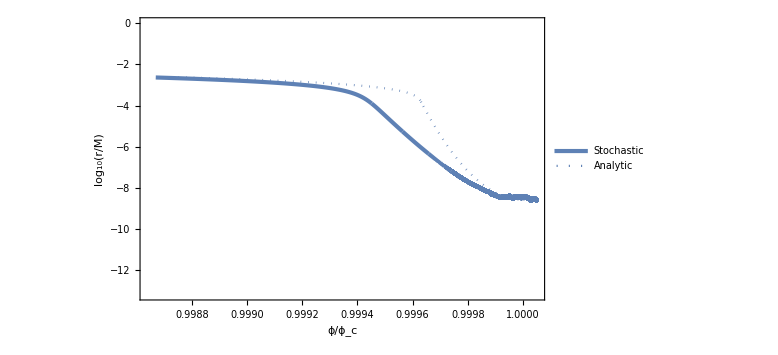

```mathematica
SamplePath5=Show[ListPlot[{phivschi5,{{1,-30}}},FrameLabel->{{"log_10(r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, water]==5}]}},PlotLegends->Placed[LineLegend[{"Stochastic","Analytic"},LegendLayout->"Row",LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.4,0.2}],PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}],
ParametricPlot[{E^ξ,Log10[ψ0[5]Exp[χξ[ξ,5]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[1]}]]
```

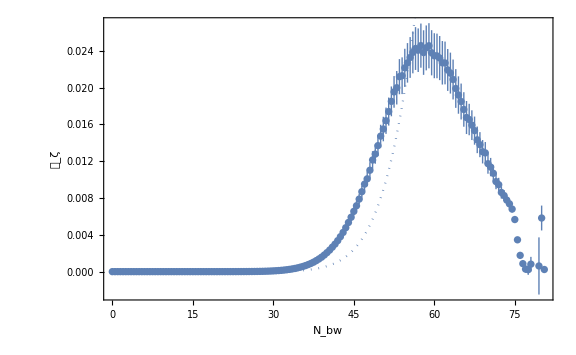

```mathematica
Show[ListPlot[meancalP5,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Plot[calPCG[NN,5],{NN,0,2(N1[5]+N2[5])},PlotStyle->{Dotted},PlotRange->Full]]
```

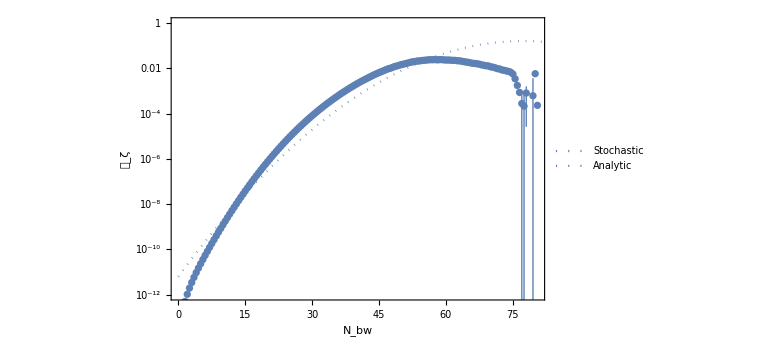

```mathematica
FigcalP5=Show[ListLogPlot[meancalP5,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, bw],Row[{Π^2==Π2,",  ",Subscript[N, water]==5}]}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1}],LogPlot[calPCG[NN,5],{NN,0,2(N1[5]+N2[5])},PlotStyle->{Dotted}],LogPlot[{0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.6,0.2}]]]
```

```mathematica
Export["calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x]//Simplify;
Vy[x_,y_]=D[V[x,y], y]//Simplify;
```

```mathematica
clsol=NDSolve[{x'[NN]==-Vx[x[NN],y[NN]]/V[x[NN],y[NN]]UnitStep[Log[x[NN]/ϕc]-ξend],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]] UnitStep[Log[x[NN]/ϕc]-ξend],x[0]==ϕc,y[0]==ψ0[1]},{x[NN],y[NN]},{NN,0,N1[1]+N2[1]},WorkingPrecision->30][[1]];
```

```mathematica
phicl[NN_]=x[NN]/.clsol;
psicl[NN_]=y[NN]/.clsol;
```

```mathematica
Show[ParametricPlot[{phicl[NN]/ϕc,Log10[psicl[NN]/M]},{NN,0,N1[1]+N2[1]},PlotRange->Full],ParametricPlot[{E^ξ,Log10[ψ0[DwList[[1]]]Exp[χξ[ξ,DwList[[1]]]]/M]},{ξ,ξend,0},PlotRange->Full,PlotStyle->{Color[2],Dashed}],ListPlot[phivschi[[1]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

### search

```mathematica
maxPdata=Import["StocDeltaN/data/maxPdata.dat"]//Sort;
```

```mathematica
LogNmaxList=Map[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]]}&,maxPdata];
LogPmaxList=Map[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[4]]]}&,maxPdata];
```

```mathematica
LogNmaxint[logPi2_,logDw_]=Interpolation[LogNmaxList][logPi2,logDw];
LogPmaxint[logPi2_,logDw_]=Interpolation[LogPmaxList][logPi2,logDw];
```

```mathematica
Sqrt[50]//N
Sqrt[2000]//N
```

7.07107

44.7214

```mathematica
FigNbwmax=ContourPlot[10^LogNmaxint[2Log10[PP],logDw],{PP,Sqrt[50],Sqrt[2000]},{logDw,Log10[1],Log10[1000]},FrameLabel->{Π,Subscript[N, water]},PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[N, bw]^max],Contours->Table[Nbw,{Nbw,10,55,5}],FrameTicks->{{Map[{Log10[#],#}&,{1,2,5,10,20,50,100,200,500,1000}],Map[{Log10[#],""}&,{1,2,5,10,20,50,100,200,500,1000}]},Automatic}]
```

-Graphics-

```mathematica
FigPmax=ContourPlot[LogPmaxint[2Log10[PP],logDw],{PP,Sqrt[50],Sqrt[2000]},{logDw,Log10[1],Log10[1000]},FrameLabel->{Π,Subscript[N, water]},PlotLegends->BarLegend[Automatic,LegendLabel->"log_10𝒫_ζ^max"],Contours->Table[logP,{logP,-4,-1,0.5}],FrameTicks->{{Map[{Log10[#],#}&,{1,2,5,10,20,50,100,200,500,1000}],Map[{Log10[#],""}&,{1,2,5,10,20,50,100,200,500,1000}]},Automatic}]
```

-Graphics-

```mathematica
Export["Nbwmax.pdf",FigNbwmax];
Export["Pmax.pdf",FigPmax];
```

```mathematica
NmaxList=Map[{Sqrt[#[[1]]],Log[#[[2]]],#[[3]]}&,maxPdata];
```

```mathematica
Log[50/1000]//N
```

-2.99573

```mathematica
FindFit[LogNmaxList,{Log10[a 10^(logP2/2) Sqrt[b+1/2 Log[10^(logP2/2)/10^logD]]],a>0,b>2},{a,b},{logP2,logD}]
```

{a→0.206673,b→38.5014}

```mathematica
Nfit[PP_,logDw_]=a PP Sqrt[b+1/2 Log[PP/10^logDw]]/.FindFit[LogNmaxList,{Log10[a 10^(logP2/2) Sqrt[b+1/2 Log[10^(logP2/2)/10^logD]]],a>0,b>2},{a,b},{logP2,logD}]
```

0.206673 PP √(38.5014+1/2 Log[10^-logDw PP])

```mathematica
ContourPlot[Nfit[PP,logDw],{PP,Sqrt[50],Sqrt[2000]},{logDw,Log10[1],Log10[1000]},FrameLabel->{Π,Subscript[N, water]},PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[N, bw]^max],Contours->Table[Nbw,{Nbw,10,50,5}],FrameTicks->{{Map[{Log10[#],#}&,{1,2,5,10,20,50,100,200,500,1000}],Map[{Log10[#],""}&,{1,2,5,10,20,50,100,200,500,1000}]},Automatic}]
```

-Graphics-

```mathematica
FindFit[LogPmaxList,{Log10[a 10^(logP2/2)/10^logD/(b+1/2 Log[10^(logP2/2)/10^logD])],a>0,b>2},{a,b},{logP2,logD}]
```

{a→0.150623,b→30.9106}

```mathematica
Pmaxfit[PP_,logD_]=a PP/10^logD/(b+1/2 Log[PP/10^logD])/.FindFit[LogPmaxList,{Log10[a 10^(logP2/2)/10^logD/(b+1/2 Log[10^(logP2/2)/10^logD])],a>0,b>2},{a,b},{logP2,logD}]
```

(0.150623 10^-logD PP)/(30.9106+1/2 Log[10^-logD PP])

```mathematica
Pmaxfit[100,Log10[10]]
```

0.0469788

```mathematica
ContourPlot[Log10[Pmaxfit[PP,logDw]],{PP,Sqrt[50],Sqrt[2000]},{logDw,Log10[1],Log10[1000]},FrameLabel->{Π,Subscript[N, water]},PlotLegends->BarLegend[Automatic,LegendLabel->"log_10𝒫_ζ^max"],Contours->Table[logP,{logP,-4,-1,0.5}],FrameTicks->{{Map[{Log10[#],#}&,{1,2,5,10,20,50,100,200,500,1000}],Map[{Log10[#],""}&,{1,2,5,10,20,50,100,200,500,1000}]},Automatic}]
```

-Graphics-

## Fitting

### Pi2 = 50

```mathematica
Π2=50;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

25000 √2

(63 π^2)/3125000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
AbsoluteTiming[fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];]
```

{29.1283,Null}

```mathematica
datared=10;
```

```mathematica
AbsoluteTiming[f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];]
```

{16.998,Null}

```mathematica
AbsoluteTiming[f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];]
```

{6.65973,Null}

```mathematica
f1int[ϕc,-5]
```

{5.54727,5.81629,5.99418,6.1038}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(1000000000 √10)

Log[(100000 √(10/21))/(√Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.72064

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-200 ξ))

-50+Re[(3750 2^(1/3) (1+ⅈ √3))/((6750000+√(-45562500000000+(6750000-50625 Log[(100000 √(10/21))/(√Dw π^(1/4))])^2)-50625 Log[(100000 √(10/21))/(√Dw π^(1/4))])^(1/3))+((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-50625 Log[(100000 √(10/21))/(√Dw π^(1/4))])^2)-50625 Log[(100000 √(10/21))/(√Dw π^(1/4))])^(1/3))/(6 2^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.00249962

-0.0025

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];(*Apeak Exp[-2 4/Π2((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)];*)
```

```mathematica
phimin={0.1409,0.141,0.141,0.141};
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {251/(1250 √2),Log[(√21 π^(1/4))/(10000000000 √10)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{36.8248,36.2759,35.8096,35.259}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin[[Dwi]]/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨OverHat[𝒩]⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {251/(1250 √2),Log[(√21 π^(1/4))/(10000000000 √10)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin[[Dwi]]/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ(𝒩̂)^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {251/(1250 √2),Log[(√21 π^(1/4))/(10000000000 √10)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Do[Export["N_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000,"Stochastic","Analytic"(*,"Ghost"*)},LegendLayout->{"Row",3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.7,0.8}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
Table[ParametricPlot[{E^ξ,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_eta2_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[𝒩, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.35,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}],
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.35,0.2}]]]
```

-Graphics-

```mathematica
Export["calP_eta2fit_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Π2/4//N
N1[Dw]^2/χ2[Dw]/.{Dw->1}//N
N1[Dw]^2/χ2[Dw]/.{Dw->10}//N
N1[Dw]^2/χ2[Dw]/.{Dw->100}//N
N1[Dw]^2/χ2[Dw]/.{Dw->1000}//N
((Sqrt[Π2]/2 Sqrt[χ2[Dw]]-Π2/(12 μ2^2)χ2[Dw])^2)/χ2[Dw]/.{Dw->1}//N
```

12.5

11.6289

11.6719

11.7179

11.7678

11.5481

### Pi2 = 100

```mathematica
Π2=100;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

50000 √2

(63 π^2)/12500000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{8.41273,8.44471,8.47126,8.49338}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/2)^(1/4))/(2000000000 √5)

Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.75231

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-400 ξ))

-50+Re[(3750 2^(1/3) (1+ⅈ √3))/((6750000+√(-45562500000000+(6750000-101250 Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])^2)-101250 Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])^(1/3))+((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-101250 Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])^2)-101250 Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])^(1/3))/(6 2^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.00182889

-0.0025

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];
```

```mathematica
phimin=0.141;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {501/(2500 √2),Log[(√(21/5) (π/2)^(1/4))/20000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{42.4448,41.3512,40.5315,39.675}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨OverHat[𝒩]⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {501/(2500 √2),Log[(√(21/5) (π/2)^(1/4))/20000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ(𝒩̂)^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {501/(2500 √2),Log[(√(21/5) (π/2)^(1/4))/20000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000,"Stochastic","Analytic"(*,"Ghost"*)},LegendLayout->{"Row",3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.7,0.8}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
Table[ParametricPlot[{E^ξ,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_eta2_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[𝒩, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.45,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}],
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.45,0.2}]]]
```

-Graphics-

```mathematica
Export["calP_eta2fit_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

### Pi2 = 200

```mathematica
Π2=200;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

100000 √2

(63 π^2)/50000000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{11.3121,11.3223,11.3318,11.3406}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(4000000000 √5)

Log[(200000 √(5/21))/(√Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.78361

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-800 ξ))

-50+Re[((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-202500 Log[(200000 √(5/21))/(√Dw π^(1/4))])^2)-202500 Log[(200000 √(5/21))/(√Dw π^(1/4))])^(1/3))/(6 2^(1/3))+(25 10^(2/3) (1+ⅈ √3))/((100-3 Log[(200000 √(5/21))/(√Dw π^(1/4))]+√3 √(Log[(200000 √(5/21))/(√Dw π^(1/4))] (-200+3 Log[(200000 √(5/21))/(√Dw π^(1/4))])))^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.00134887

-0.0025

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];
```

```mathematica
phimin=0.141;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {1001/(5000 √2),Log[(√21 π^(1/4))/(40000000000 √5)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{49.3919,47.9019,46.78,45.6119}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨OverHat[𝒩]⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {1001/(5000 √2),Log[(√21 π^(1/4))/(40000000000 √5)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ(𝒩̂)^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {1001/(5000 √2),Log[(√21 π^(1/4))/(40000000000 √5)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000,"Stochastic","Analytic"(*,"Ghost"*)},LegendLayout->{"Row",3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.3,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
Table[ParametricPlot[{E^ξ,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_eta2_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[𝒩, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.5,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}],
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.5,0.2}]]]
```

-Graphics-

```mathematica
Export["calP_eta2fit_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

### Pi2 = 500

```mathematica
Π2=500;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

250000 √2

(63 π^2)/312500000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{15.9638,15.9678,15.9715,15.9751}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/10)^(1/4))/10000000000

Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.82445

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-2000 ξ))

-50+Re[((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-506250 Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))])^2)-506250 Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))])^(1/3))/(6 2^(1/3))+(50 5^(1/3) (1+ⅈ √3))/((40-3 Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))]+√3 √(Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))] (-80+3 Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))])))^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.000915214

-0.0025

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];
```

```mathematica
phimin=0.141;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {2501/(12500 √2),Log[(√21 (π/10)^(1/4))/100000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{62.2409,60.1042,58.488,56.8022}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨OverHat[𝒩]⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {2501/(12500 √2),Log[(√21 (π/10)^(1/4))/100000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ(𝒩̂)^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {2501/(12500 √2),Log[(√21 (π/10)^(1/4))/100000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000,"Stochastic","Analytic"(*,"Ghost"*)},LegendLayout->{"Row",3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.3,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
Table[ParametricPlot[{E^ξ,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_eta2_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[𝒩, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}],
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.6,0.2}]]]
```

-Graphics-

```mathematica
Export["calP_eta2fit_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

### Pi2 = 1000

```mathematica
Π2=1000;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

500000 √2

(63 π^2)/1250000000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];
```

```mathematica
datared=10;
```

```mathematica
f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];
```

```mathematica
f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
```

```mathematica
f1int[ϕc,-5]
```

{20.0186,20.0209,20.0232,20.0253}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/20000000000

Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.85497

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-4000 ξ))

-50+Re[(3750 2^(1/3) (1+ⅈ √3))/((6750000+√(-45562500000000+(6750000-1012500 Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))])^2)-1012500 Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))])^(1/3))+((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-1012500 Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))])^2)-1012500 Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))])^(1/3))/(6 2^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.000690903

-0.0025

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];
```

```mathematica
phimin=0.141;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {5001/(25000 √2),Log[(√21 (π/5)^(1/4))/200000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{75.5178,72.7997,70.7354,68.5766}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨OverHat[𝒩]⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {5001/(25000 √2),Log[(√21 (π/5)^(1/4))/200000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ(𝒩̂)^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {5001/(25000 √2),Log[(√21 (π/5)^(1/4))/200000000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000,"Stochastic","Analytic"(*,"Ghost"*)},LegendLayout->{"Row",3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.3,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}],
Table[ParametricPlot[{E^ξ,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}],PlotRange->Full]
```

-Graphics-

```mathematica
Export["samples_eta2_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[𝒩, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.7,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}],
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.7,0.2}]]]
```

-Graphics-

```mathematica
Export["calP_eta2fit_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

### Pi2 = 2000

```mathematica
Π2=2000;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

1000000 √2

(63 π^2)/5000000000000000000000

```mathematica
DwList={1,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
AbsoluteTiming[fndata=Table[Sort[Select[Import["StocDeltaN/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];]
```

{485.661,Null}

```mathematica
datared=10;
```

```mathematica
AbsoluteTiming[f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{trajdata[[Dwi,i,2]]/ϕc,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];]
```

{154.848,Null}

```mathematica
AbsoluteTiming[f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];]
```

{91.4505,Null}

```mathematica
f1int[ϕc,-5]
```

{24.2124,24.2139,24.2154,24.2168}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/(20000000000 2^(3/4))

Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)]

```mathematica
Sqrt[χ2[1000]]//N
```

2.88515

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-8000 ξ))

5/2 (-20+Re[(10 10^(1/3) (1+ⅈ √3))/((10+(√(-45562500000000+(6750000-2025000 Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)])^2))/675000-3 Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)])^(1/3))+10^(2/3) (1-ⅈ √3) (10+(√(-45562500000000+(6750000-2025000 Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)])^2))/675000-3 Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)])^(1/3)])

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-0.00052726

-0.0025

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];(*Apeak Exp[-2 4/Π2((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)];*)
```

```mathematica
phimin=0.141;
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-3;
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {10001/(50000 √2),Log[(√21 (π/5)^(1/4))/(200000000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{92.4385,89.0914,86.5391,83.8622}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨OverHat[𝒩]⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {10001/(50000 √2),Log[(√21 (π/5)^(1/4))/(200000000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[ϕ ϕc,logr+Log10[M]][[Dwi]],{ϕ,phimin/ϕc,phimax/ϕc},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Row[{Π^2==Π2,",  ",Subscript[N, ψ]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ(𝒩̂)^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}}],
ParametricPlot[{E^ξ,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {10001/(50000 √2),Log[(√21 (π/5)^(1/4))/(200000000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,4}]
Do[Export["dN2_eta2_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,4}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"ϕ/ϕ_(<c>)",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000,"Stochastic","Analytic"(*,"Ghost"*)},LegendLayout->{"Row",3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.3,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}}(*,GridLines->{None,{Log10[(ψ0[Dw]Exp[χ2[Dw]])/M]/.{Dw->100}}}*)],
Table[ParametricPlot[{E^ξ,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}],PlotRange->Full]
```

-Graphics-

```mathematica
Export["samples_eta2_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[𝒩, bw],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Subscript[N, ψ]==1,Subscript[N, ψ]==10,Subscript[N, ψ]==100,Subscript[N, ψ]==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.7,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}],
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.7,0.2}]]]
```

-Graphics-

```mathematica
Export["calP_eta2fit_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Π2/4
N1[Dw]^2/χ2[Dw]/.{Dw->1}//N
N1[Dw]^2/χ2[Dw]/.{Dw->10}//N
N1[Dw]^2/χ2[Dw]/.{Dw->100}//N
N1[Dw]^2/χ2[Dw]/.{Dw->1000}//N
((Sqrt[Π2]/2 Sqrt[χ2[Dw]]-Π2/(12 μ2^2)χ2[Dw])^2)/χ2[Dw]/.{Dw->10}//N
```

500

350.115

354.776

359.891

365.563

286.543

```mathematica
(NPTint[Π2,Dw]^2+2/(3 μ2^2)NPTint[Π2,Dw]^3)/N1[Dw]^2/.{Dw->100}
(NPTint[Π2,Dw]^2+2/(3 μ2^2)NPTint[Π2,Dw]^3)/(Π2/4 χ2[Dw])/.{Dw->100}
```

1.23748

0.890715

```mathematica
(Sqrt[Π2]/2 Sqrt[χ2[Dw]]-Π2/(12 μ2^2)χ2[Dw])/NPTint[Π2,Dw]/.{Dw->100}
N1[Dw]/NPTint[Π2,Dw]/.{Dw->100}
```

0.955651

1.05218

```mathematica
χ2[Dw]/(4/Π2(N1[Dw]^2+2/(3 μ2^2)N1[Dw]^3))/.{Dw->100}//N
χ2[Dw]/(4/Π2(NPTint[Π2,Dw]^2+2/(3 μ2^2)NPTint[Π2,Dw]^3))/.{Dw->100}//N
(NPTint[Π2,Dw]^2+2/(3 μ2^2)NPTint[Π2,Dw]^3)/N1[Dw]^2/.{Dw->100}
(N1[Dw]^2+2/(3 μ2^2)N1[Dw]^3)/N1[Dw]^2/.{Dw->100}//N
```

1.

1.12269

1.23748

1.38931

## EoI

### Pi2 = 50

```mathematica
Π2=50;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

25000 √2

(63 π^2)/3125000000000000000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(1000000000 √10)

Log[(100000 √(10/21))/(√Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-1/50+20000 y^2))/3125000000000000000,(63 π^2 x y)/78125000000000},{(63 π^2 x y)/78125000000000,(63 π^2 (-1+50 x^2+300 y^2))/7812500000000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-(63 π^2 (20001-1000000 x^2-7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/312500000000000000000,(63 π^2 (-20001+1000000 x^2+7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/312500000000000000000}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,10,100,1000};
```

```mathematica
Nf={12,11.5,11,10};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{11.0608732237836936498883441289,10.7830601603219074245450000077,10.3495877290976631132469147064,9.81607290891796922762361695642}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {11.0608732237836936498883441289} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.7830601603219074245450000077} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.00250708588637734860617779352,-0.00250911481254534681762379114,-0.00251213462396079985982561274,-0.00251561163235895223395243701}

-0.0025

{-0.00249962,-0.0023551,-0.00220271,-0.0020408}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {10.0609} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {11.0608732237836936498883441289} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[50]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {11.0608732237836936498883441289} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.667746503534577577277766×10^-8,3.016263988511481027414518×10^-8,5.026713782850900233427575×10^-8,7.346499279027915897888615×10^-8}

```mathematica
Show[Table[ParametricPlot[{xsol[NN][[Dw]],Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 100

```mathematica
Π2=100;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

50000 √2

(63 π^2)/12500000000000000000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/2)^(1/4))/(2000000000 √5)

Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-1+1000000 y^2))/625000000000000000000,(63 π^2 x y)/312500000000000},{(63 π^2 x y)/312500000000000,(63 π^2 (-1+50 x^2+300 y^2))/31250000000000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-(63 π^2 (20001-1000000 x^2-7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/1250000000000000000000,(63 π^2 (-20001+1000000 x^2+7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/1250000000000000000000}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,10,100,1000};
```

```mathematica
Nf={17,16,15.5,14.5};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{16.6172352316340006522187632693,15.8948633940576570314965031351,15.1215183933717140835772774443,14.2887555430278211674031826671}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {16.6172352316340006522187632693} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.0025206862048730555650420647,-0.0025229891001900587185441691,-0.0025252773624924122351847911,-0.00252754383538252306982556324}

-0.0025

{-0.00182889,-0.0017229,-0.00161145,-0.00149342}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {15.6173} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {16.6172352316340006522187632693} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[Π2]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {16.6172352316340006522187632693} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.02381535735930905091031×10^-7,1.17821830706233821071852×10^-7,1.33187059293695729256552×10^-7,1.484286195286848005170784×10^-7}

```mathematica
Show[Table[ParametricPlot[{xsol[NN][[Dw]],Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 200

```mathematica
Π2=200;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

100000 √2

(63 π^2)/50000000000000000000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(4000000000 √5)

Log[(200000 √(5/21))/(√Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-1/50+20000 y^2))/50000000000000000000,(63 π^2 x y)/1250000000000000},{(63 π^2 x y)/1250000000000000,(63 π^2 (-1+50 x^2+300 y^2))/125000000000000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-(63 π^2 (20001-1000000 x^2-7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/5000000000000000000000,(63 π^2 (-20001+1000000 x^2+7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/5000000000000000000000}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,10,100,1000};
```

```mathematica
Nf={24,23,22,20.5};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{23.490872211793903814795116718,22.4959509346357179973043107991,21.4366449784800976788286479821,20.3004410582431942951687094169}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {23.490872211793903814795116718} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.0025306686402410640893637386,-0.00253203957782117439567735706,-0.00253338423616188025871059184,-0.0025347010039425549517427586}

-0.0025

{-0.00134887,-0.00127024,-0.00118778,-0.00110075}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {22.4909} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {23.490872211793903814795116718} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[Π2]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {23.490872211793903814795116718} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.66951724246109342038347×10^-7,1.76199357956503818914259×10^-7,1.852777346648756232164013×10^-7,1.94175496480848611545322×10^-7}

```mathematica
Show[Table[ParametricPlot[{xsol[NN][[Dw]],Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 500

```mathematica
Π2=500;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

250000 √2

(63 π^2)/312500000000000000000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/10)^(1/4))/10000000000

Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-1/50+20000 y^2))/312500000000000000000,(63 π^2 x y)/7812500000000000},{(63 π^2 x y)/7812500000000000,(63 π^2 (-1+50 x^2+300 y^2))/781250000000000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-(63 π^2 (20001-1000000 x^2-7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/31250000000000000000000,(63 π^2 (-20001+1000000 x^2+7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/31250000000000000000000}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,10,100,1000};
```

```mathematica
Nf={36.5,35,33.5,32};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{36.2151673767521213000511907353,34.7839680828784926754020394151,33.2580318303004878612064716875,31.6190032808702462993139852631}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {36.2151673767521213000511907353} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.0025375174169566196445620037,-0.0025382297717338145858317122,-0.00253892145202816941238773532,-0.0025395916436048469321974735}

-0.0025

{-0.000915214,-0.000861216,-0.000804796,-0.000745493}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {35.2152} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {36.2151673767521213000511907353} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[Π2]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {36.2151673767521213000511907353} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{2.11711699095494980742684×10^-7,2.16536820842888787305168×10^-7,2.21224034343597052321085×10^-7,2.25767630063171020782995×10^-7}

```mathematica
Show[Table[ParametricPlot[{xsol[NN][[Dw]],Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 1000

```mathematica
Π2=1000;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

500000 √2

(63 π^2)/1250000000000000000000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/20000000000

Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-1+1000000 y^2))/62500000000000000000000,(63 π^2 x y)/31250000000000000},{(63 π^2 x y)/31250000000000000,(63 π^2 (-1+50 x^2+300 y^2))/3125000000000000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-(63 π^2 (20001-1000000 x^2-7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/125000000000000000000000,(63 π^2 (-20001+1000000 x^2+7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/125000000000000000000000}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,10,100,1000};
```

```mathematica
Nf={49.5,48,46,44};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{49.3787085191415587469237298157,47.5560016192843690511783895722,45.6078494512997360302243444219,43.5100950620749300584513315091}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {49.3787085191415587469237298157} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.0025401086306164713318095397,-0.0025405714286759569578909065,-0.0025410170971724225129252732,-0.0025414450877494478896026991}

-0.0025

{-0.000690903,-0.000649709,-0.000606771,-0.000561773}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {48.3787} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {49.3787085191415587469237298157} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[Π2]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {49.3787085191415587469237298157} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{2.28766528665948819605862×10^-7,2.31906197361381303362395×10^-7,2.34930545360228809637216×10^-7,2.37835749435998054537125×10^-7}

```mathematica
Show[Table[ParametricPlot[{xsol[NN][[Dw]],Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 2000

```mathematica
Π2=2000;
As=21 10^-10;
M=1/10;
ϕc=Sqrt[2]/10;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

1000000 √2

(63 π^2)/5000000000000000000000

```mathematica
1/(μ1 10 ϕc)//N
```

5.×10^-7

```mathematica
(1-0.1409/ϕc)μ1 10 ϕc
```

7373.09

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/(20000000000 2^(3/4))

Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-1/50+20000 y^2))/5000000000000000000000,(63 π^2 x y)/125000000000000000},{(63 π^2 x y)/125000000000000000,(63 π^2 (-1+50 x^2+300 y^2))/12500000000000000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-(63 π^2 (20001-1000000 x^2-7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/500000000000000000000000,(63 π^2 (-20001+1000000 x^2+7000000 y^2+√(1000000000000 x^4+(19999-5000000 y^2)^2+2000000 x^2 (-19999+13000000 y^2))))/500000000000000000000000}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,10,100,1000};
```

```mathematica
Nf={66.5,64,62,59};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{66.161048108764427212809837067,63.9159484090252708757021510237,61.5086963576401912472116802652,58.9080598257383780613395332954}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/8;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {66.161048108764427212809837067} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.00254155593359736157148893488,-0.0025418785736074508124433803,-0.0025421865382013527036733275,-0.0025424794530211880411973258}

-0.00125

{-0.00052726,-0.00049551,-0.000462487,-0.000427966}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {65.1611} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {66.161048108764427212809837067} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[2000]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {66.161048108764427212809837067} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{2.38334465932445172035029×10^-7,2.40525205218936329636228×10^-7,2.42616723741587919911058×10^-7,2.44606418868364919924841×10^-7}

```mathematica
Show[Table[ParametricPlot[{xsol[NN][[Dw]],Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### EoI

```mathematica
Pi2List={50,100,200,500,1000,2000};
DwList={1,10,100,1000};
```

```mathematica
EoIList=Flatten[Table[{Pi2List[[i]],DwList[[j]],Vend[Pi2List[[i]]][[j]]},{i,Length[Pi2List]},{j,Length[DwList]}],1]
```

{{50,1,1.667746503534577577277766×10^-8},{50,10,3.016263988511481027414518×10^-8},{50,100,5.026713782850900233427575×10^-8},{50,1000,7.346499279027915897888615×10^-8},{100,1,1.02381535735930905091031×10^-7},{100,10,1.17821830706233821071852×10^-7},{100,100,1.33187059293695729256552×10^-7},{100,1000,1.484286195286848005170784×10^-7},{200,1,1.66951724246109342038347×10^-7},{200,10,1.76199357956503818914259×10^-7},{200,100,1.852777346648756232164013×10^-7},{200,1000,1.94175496480848611545322×10^-7},{500,1,2.11711699095494980742684×10^-7},{500,10,2.16536820842888787305168×10^-7},{500,100,2.21224034343597052321085×10^-7},{500,1000,2.25767630063171020782995×10^-7},{1000,1,2.28766528665948819605862×10^-7},{1000,10,2.31906197361381303362395×10^-7},{1000,100,2.34930545360228809637216×10^-7},{1000,1000,2.37835749435998054537125×10^-7},{2000,1,2.38334465932445172035029×10^-7},{2000,10,2.40525205218936329636228×10^-7},{2000,100,2.42616723741587919911058×10^-7},{2000,1000,2.44606418868364919924841×10^-7}}

```mathematica
EoIList//MatrixForm
```

(50 | 1 | 1.667746503534577577277766×10^-8
50 | 10 | 3.016263988511481027414518×10^-8
50 | 100 | 5.026713782850900233427575×10^-8
50 | 1000 | 7.346499279027915897888615×10^-8
100 | 1 | 1.02381535735930905091031×10^-7
100 | 10 | 1.17821830706233821071852×10^-7
100 | 100 | 1.33187059293695729256552×10^-7
100 | 1000 | 1.484286195286848005170784×10^-7
200 | 1 | 1.66951724246109342038347×10^-7
200 | 10 | 1.76199357956503818914259×10^-7
200 | 100 | 1.852777346648756232164013×10^-7
200 | 1000 | 1.94175496480848611545322×10^-7
500 | 1 | 2.11711699095494980742684×10^-7
500 | 10 | 2.16536820842888787305168×10^-7
500 | 100 | 2.21224034343597052321085×10^-7
500 | 1000 | 2.25767630063171020782995×10^-7
1000 | 1 | 2.28766528665948819605862×10^-7
1000 | 10 | 2.31906197361381303362395×10^-7
1000 | 100 | 2.34930545360228809637216×10^-7
1000 | 1000 | 2.37835749435998054537125×10^-7
2000 | 1 | 2.38334465932445172035029×10^-7
2000 | 10 | 2.40525205218936329636228×10^-7
2000 | 100 | 2.42616723741587919911058×10^-7
2000 | 1000 | 2.44606418868364919924841×10^-7)

```mathematica
Export["StocDeltaN/EoI.dat",EoIList];
```

## M = 10^16 GeV

## EoI

### Pi2 = 50

```mathematica
Π2=50;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

2887532575/(4 √2)

(63 π^2)/651394091537978955078125000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(14437662875000 √10)

Log[(100000 √(10/21))/(√Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-4+1406228364025 y^2))/130278818307595791015625000000,(63 π^2 x y)/46322070312500000},{(63 π^2 x y)/46322070312500000,(63 π^2 (-8+237169 x^2+1423014 y^2))/21972318187890625000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-1/260557636615191582031250000000 63 π^2 (47433804-1406228364025 x^2-9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2))),1/260557636615191582031250000000 63 π^2 (-47433804+1406228364025 x^2+9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2)))}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
Nf={12,12.05,11.5,11,10};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηϕsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[1,1]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{-ηψsol[NN][[Dw]],-ηϕsol[NN][[Dw]]},{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dashed,Color[Dw]}},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{11.0463568292280973955901532494,10.938767348406920491614304586,10.7694654367275794639300020766,10.3365751835998833380865078934,9.80375921975076834392194010749}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {11.0463568292280973955901532494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.938767348406920491614304586} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-4.21642270204120384683293×10^-6,-4.21642487896553860083965×10^-6,-4.21642824367639576255249×10^-6,-4.2164365118770331431123×10^-6,-4.21644603766740443674248×10^-6}

-4.2164×10^-6

{-4.21577×10^-6,-4.10098×10^-6,-3.97202×10^-6,-3.715×10^-6,-3.44193×10^-6}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {10.0464} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {11.0463568292280973955901532494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[50]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {11.0463568292280973955901532494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{7.9542406137007300921247×10^-17,1.040190353141739025348×10^-16,1.418507912573797395524×10^-16,2.348160655532469621079×10^-16,3.419216944454546145341×10^-16}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 100

```mathematica
Π2=100;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

2887532575/(2 √2)

(63 π^2)/2605576366151915820312500000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/2)^(1/4))/(28875325750000 √5)

Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-4+1406228364025 y^2))/521115273230383164062500000000,(63 π^2 x y)/185288281250000000},{(63 π^2 x y)/185288281250000000,(63 π^2 (-8+237169 x^2+1423014 y^2))/87889272751562500000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-((63 π^2 (47433804-1406228364025 x^2-9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2))))/1042230546460766328125000000000),1/1042230546460766328125000000000 63 π^2 (-47433804+1406228364025 x^2+9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2)))}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
Nf={17,16.9,16.5,15.5,14.5};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{16.5931604835013665992789213668,16.2567812864031975944672888951,15.8776802412529244593364490663,15.1062402827068880795716102272,14.2747480001764884278591352969}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {16.5931604835013665992789213668} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-4.2164599796045306362244×10^-6,-4.21646297789391541791798×10^-6,-4.21646624149175277025305×10^-6,-4.21647251340869202018835×10^-6,-4.21647873520970700458571×10^-6}

-4.2164×10^-6

{-3.08453×10^-6,-3.0003×10^-6,-2.90578×10^-6,-2.71781×10^-6,-2.51875×10^-6}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {15.5932} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {16.5931604835013665992789213668} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[Π2]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {16.5931604835013665992789213668} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{4.746948205088901201275×10^-16,5.084070963156270530728×10^-16,5.451025024144381793128×10^-16,6.156231315799944575094×10^-16,6.855804364618673127778×10^-16}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 200

```mathematica
Π2=200;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

2887532575/(√2)

(63 π^2)/10422305464607663281250000000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(57750651500000 √5)

Log[(200000 √(5/21))/(√Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-4+1406228364025 y^2))/2084461092921532656250000000000,(63 π^2 x y)/741153125000000000},{(63 π^2 x y)/741153125000000000,(63 π^2 (-8+237169 x^2+1423014 y^2))/351557091006250000000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-((63 π^2 (47433804-1406228364025 x^2-9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2))))/4168922185843065312500000000000),1/4168922185843065312500000000000 63 π^2 (-47433804+1406228364025 x^2+9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2)))}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
Nf={24,23.5,23,21.9,20.8};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{23.4589737226674105217117020429,22.9947448314321297028563087288,22.4755797043197659185569578213,21.4189581141617404069822922963,20.2846018074693696384770377621}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {23.4589737226674105217117020429} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-4.21648735184596253603481×10^-6,-4.21648914689839754774917×10^-6,-4.21649107866761147298882×10^-6,-4.21649477080591453199236×10^-6,-4.21649839157241262327786×10^-6}

-4.2164×10^-6

{-2.27495×10^-6,-2.21241×10^-6,-2.14233×10^-6,-2.00327×10^-6,-1.85648×10^-6}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {22.459} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {23.4589737226674105217117020429} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[Π2]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {23.4589737226674105217117020429} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{7.70471588791012453745×10^-16,7.90655073455394638748×10^-16,8.12375811112726229476×10^-16,8.538901162545961210917×10^-16,8.946019775540502453675×10^-16}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 500

```mathematica
Π2=500;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

14437662875/(2 √2)

(63 π^2)/65139409153797895507812500000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/10)^(1/4))/144376628750000

Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-4+1406228364025 y^2))/13027881830759579101562500000000,(63 π^2 x y)/4632207031250000000},{(63 π^2 x y)/4632207031250000000,(63 π^2 (-8+237169 x^2+1423014 y^2))/2197231818789062500000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-((63 π^2 (47433804-1406228364025 x^2-9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2))))/26055763661519158203125000000000),(63 π^2 (-47433804+1406228364025 x^2+9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2))))/26055763661519158203125000000000}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
Nf={36.7,36,35,33.5,32};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{36.186339502537811695195550198,35.5068758809898836247470459391,34.7452253340271537237411467294,33.234775360419254280091214796,31.599200564689122136167453726}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {36.186339502537811695195550198} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-4.21650614137163086084552×10^-6,-4.21650709518552683882404×10^-6,-4.21650811745617782054901×10^-6,-4.21651000439039833057282×10^-6,-4.21651184913558635475419×10^-6}

-4.2164×10^-6

{-1.54356×10^-6,-1.50058×10^-6,-1.45249×10^-6,-1.35734×10^-6,-1.25732×10^-6}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {35.1864} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {36.186339502537811695195550198} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[Π2]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {36.186339502537811695195550198} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{9.74544570119111157093×10^-16,9.852692846847698291872×10^-16,9.96763733726169824517×10^-16,1.017980504149484187413×10^-15,1.03872291455449860154×10^-15}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 1000

```mathematica
Π2=1000;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

14437662875/(√2)

(63 π^2)/260557636615191582031250000000

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/288753257500000

Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-4+1406228364025 y^2))/52111527323038316406250000000000,(63 π^2 x y)/18528828125000000000},{(63 π^2 x y)/18528828125000000000,(63 π^2 (-8+237169 x^2+1423014 y^2))/8788927275156250000000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-((63 π^2 (47433804-1406228364025 x^2-9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2))))/104223054646076632812500000000000),(63 π^2 (-47433804+1406228364025 x^2+9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2))))/104223054646076632812500000000000}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
Nf={49.5,49,48,46,44};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{49.3228495687705077216270414517,48.4909497248589732570868231823,47.5255050053546421336230241232,45.5779077349693222424481718844,43.4853140876842158894392585447}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/4;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {49.3228495687705077216270414517} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-4.21651329103541780135146×10^-6,-4.21651388866554987907623×10^-6,-4.21651454902522427401939×10^-6,-4.21651577832966099002687×10^-6,-4.2165169567239019147826×10^-6}

-4.2164×10^-6

{-1.16525×10^-6,-1.13244×10^-6,-1.09577×10^-6,-1.02336×10^-6,-9.47464×10^-7}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {48.3229} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {49.3228495687705077216270414517} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[Π2]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {49.3228495687705077216270414517} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.05253696203350400921×10^-15,1.05925675291399717108×10^-15,1.0666818805688772651×10^-15,1.08050426575085998175×10^-15,1.0937542194306122944×10^-15}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### Pi2 = 2000

```mathematica
Π2=2000;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

14437662875 √2

(63 π^2)/1042230546460766328125000000000

```mathematica
1/(μ1 10 ϕc)//N
```

8.43281×10^-10

```mathematica
(1-0.999995)μ1 10 ϕc
```

5929.23

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/(288753257500000 2^(3/4))

Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)]

```mathematica
Htinξ[ξ_]=Simplify[Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]];
Ht1[Dw_]=Simplify[Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]]//Re;
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξin2[ξ_,Dw_]=1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw];
```

```mathematica
Vpp[x_,y_]={{D[D[V[x,y], x], x],D[D[V[x,y], y], x]},{D[D[V[x,y], x], y],D[D[V[x,y], y], y]}}//Simplify
```

{{(63 π^2 (-4+1406228364025 y^2))/208446109292153265625000000000000,(63 π^2 x y)/74115312500000000000},{(63 π^2 x y)/74115312500000000000,(63 π^2 (-8+237169 x^2+1423014 y^2))/35155709100625000000000000}}

```mathematica
Vλ[x_,y_]=Eigenvalues[Vpp[x,y]]//Simplify
```

{-((63 π^2 (47433804-1406228364025 x^2-9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2))))/416892218584306531250000000000000),(63 π^2 (-47433804+1406228364025 x^2+9843598548175 y^2+√(1977478211788427914200625 x^4+(47433796-7031141820125 y^2)^2+2812456728050 x^2 (-47433796+18280968732325 y^2))))/416892218584306531250000000000000}

```mathematica
ηλ[x_,y_]=Vλ[x,y]/V[x,y];
```

```mathematica
Vx[x_,y_]=D[V[x,y], x];
Vy[x_,y_]=D[V[x,y], y];
```

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
Nf={66.5,65.5,64,61.9,59.3};
sol=Table[NDSolve[{x'[NN]==(-Vx[x[NN],y[NN]])/V[x[NN],y[NN]],y'[NN]==(-Vy[x[NN],y[NN]])/V[x[NN],y[NN]],x[0]==ϕc,y[0]==ψ0[DwList[[Dw]]]},{x[NN],y[NN]},{NN,0,Nf[[Dw]]},WorkingPrecision->30][[1]],{Dw,Length[DwList]}]
```

{{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]},{x[NN]→InterpolatingFunction[…][NN],y[NN]→InterpolatingFunction[…][NN]}}

```mathematica
xsol[NN_]=x[NN]/.sol;
ysol[NN_]=y[NN]/.sol;
ηλsol[NN_]=Table[ηλ[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
ηψsol[NN_]=Table[(Vpp[xsol[NN][[Dw]],ysol[NN][[Dw]]][[2,2]])/V[xsol[NN][[Dw]],ysol[NN][[Dw]]],{Dw,Length[DwList]}];
```

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nf[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[{Abs[ηλsol[NN][[Dw,1]]],Abs[ηλsol[NN][[Dw,2]]]},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Color[Dw],Dashed}},GridLines->{None,{1}},FrameLabel->{𝒩,Subscript[η, λ]}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Show[Table[LogPlot[-ηψsol[NN][[Dw]],{NN,0,Nf[[Dw]]},FrameLabel->{𝒩,-Subscript[η, ψ]},PlotStyle->{AbsoluteThickness[3],Color[Dw]},GridLines->{None,{1,2}}],{Dw,Length[DwList]}]]
```

-Graphics-

```mathematica
Nend=Table[NN/.FindRoot[ηψsol[NN][[Dw]]==-2,{NN,Nf[[Dw]]-0.1},WorkingPrecision->30],{Dw,Length[DwList]}]
```

{66.1233854971895346386087481262,65.071223398867268203492220798,63.8800736113150578398457894624,61.4713053665118653810946424555,58.881219956224381801917614494}

```mathematica
ξend=Table[Log[(xsol[Nend[[Dw]]][[Dw]])/ϕc],{Dw,Length[DwList]}]
ξendanal=-M^2/8;ξendanal//N
Table[ξ2[DwList[[Dw]]]//N,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {66.1233854971895346386087481262} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-4.21651726222486130089562×10^-6,-4.21651769184874193956828×10^-6,-4.216518151942312851204×10^-6,-4.21651900256144793313855×10^-6,-4.21651980810934967642012×10^-6}

-2.1082×10^-6

{-8.89257×10^-7,-8.63956×10^-7,-8.35709×10^-7,-7.80013×10^-7,-7.2179×10^-7}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,Nend[[Dw]]-1,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],
Table[ListPlot[{{Exp[ξendanal],Log10[(ψ0[Dw]Exp[χξin2[ξendanal,Dw]])/M]}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {65.1234} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Table[LogPlot[{V[xsol[NN][[Dw]],ysol[NN][[Dw]]]/Λ4,V[ϕc Exp[ξendanal],(ψ0[DwList[[Dw]]]Exp[χξin2[ξendanal,DwList[[Dw]]]])/M]/Λ4},{NN,0,Nf[[Dw]]},PlotStyle->{{AbsoluteThickness[3],Color[Dw]},{Dotted,Color[Dw]}}],{Dw,Length[DwList]}],
Table[ListLogPlot[{{Nend[[Dw]],V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4}},Joined->False,PlotStyle->Directive[Color[Dw]]],{Dw,Length[DwList]}],PlotRange->Full,FrameLabel->{𝒩,"V/Λ^4"}]
```

InterpolatingFunction::dmval: Input value {66.1233854971895346386087481262} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Vend[2000]=Table[1-V[xsol[Nend[[Dw]]][[Dw]],ysol[Nend[[Dw]]][[Dw]]]/Λ4,{Dw,Length[DwList]}]
```

InterpolatingFunction::dmval: Input value {66.1233854971895346386087481262} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.09598991542111578041×10^-15,1.10082064071906696493×10^-15,1.10599397056267951355×10^-15,1.11555840435437159234×10^-15,1.12461605633548603696×10^-15}

```mathematica
Show[Table[ParametricPlot[{(xsol[NN][[Dw]])/ϕc,Log10[(ysol[NN][[Dw]])/M]},{NN,0,Nend[[Dw]]},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ, "c"]}],Subscript[log, 10][Row[{ψ,"/","M"}]]},PlotStyle->{AbsoluteThickness[3],Color[Dw]}],{Dw,Length[DwList]}],PlotRange->Full]
```

-Graphics-

### EoI

```mathematica
Pi2List={50,100,200,500,1000,2000};
DwList={1,3,10,100,1000};
```

```mathematica
EoIList=Flatten[Table[{Pi2List[[i]],DwList[[j]],Vend[Pi2List[[i]]][[j]]},{i,Length[Pi2List]},{j,Length[DwList]}],1]
```

{{50,1,7.9542406137007300921247×10^-17},{50,3,1.040190353141739025348×10^-16},{50,10,1.418507912573797395524×10^-16},{50,100,2.348160655532469621079×10^-16},{50,1000,3.419216944454546145341×10^-16},{100,1,4.746948205088901201275×10^-16},{100,3,5.084070963156270530728×10^-16},{100,10,5.451025024144381793128×10^-16},{100,100,6.156231315799944575094×10^-16},{100,1000,6.855804364618673127778×10^-16},{200,1,7.70471588791012453745×10^-16},{200,3,7.90655073455394638748×10^-16},{200,10,8.12375811112726229476×10^-16},{200,100,8.538901162545961210917×10^-16},{200,1000,8.946019775540502453675×10^-16},{500,1,9.74544570119111157093×10^-16},{500,3,9.852692846847698291872×10^-16},{500,10,9.96763733726169824517×10^-16},{500,100,1.017980504149484187413×10^-15},{500,1000,1.03872291455449860154×10^-15},{1000,1,1.05253696203350400921×10^-15},{1000,3,1.05925675291399717108×10^-15},{1000,10,1.0666818805688772651×10^-15},{1000,100,1.08050426575085998175×10^-15},{1000,1000,1.0937542194306122944×10^-15},{2000,1,1.09598991542111578041×10^-15},{2000,3,1.10082064071906696493×10^-15},{2000,10,1.10599397056267951355×10^-15},{2000,100,1.11555840435437159234×10^-15},{2000,1000,1.12461605633548603696×10^-15}}

```mathematica
EoIList//MatrixForm
```

(50 | 1 | 7.9542406137007300921247×10^-17
50 | 3 | 1.040190353141739025348×10^-16
50 | 10 | 1.418507912573797395524×10^-16
50 | 100 | 2.348160655532469621079×10^-16
50 | 1000 | 3.419216944454546145341×10^-16
100 | 1 | 4.746948205088901201275×10^-16
100 | 3 | 5.084070963156270530728×10^-16
100 | 10 | 5.451025024144381793128×10^-16
100 | 100 | 6.156231315799944575094×10^-16
100 | 1000 | 6.855804364618673127778×10^-16
200 | 1 | 7.70471588791012453745×10^-16
200 | 3 | 7.90655073455394638748×10^-16
200 | 10 | 8.12375811112726229476×10^-16
200 | 100 | 8.538901162545961210917×10^-16
200 | 1000 | 8.946019775540502453675×10^-16
500 | 1 | 9.74544570119111157093×10^-16
500 | 3 | 9.852692846847698291872×10^-16
500 | 10 | 9.96763733726169824517×10^-16
500 | 100 | 1.017980504149484187413×10^-15
500 | 1000 | 1.03872291455449860154×10^-15
1000 | 1 | 1.05253696203350400921×10^-15
1000 | 3 | 1.05925675291399717108×10^-15
1000 | 10 | 1.0666818805688772651×10^-15
1000 | 100 | 1.08050426575085998175×10^-15
1000 | 1000 | 1.0937542194306122944×10^-15
2000 | 1 | 1.09598991542111578041×10^-15
2000 | 3 | 1.10082064071906696493×10^-15
2000 | 10 | 1.10599397056267951355×10^-15
2000 | 100 | 1.11555840435437159234×10^-15
2000 | 1000 | 1.12461605633548603696×10^-15)

```mathematica
Export["StocDeltaN/M=1e+16GeV/EoI.dat",EoIList];
```

```mathematica
0.1409/(Sqrt[2]/10)
```

0.996313

## Fitting

### Pi2 = 50

```mathematica
Π2=50;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

2887532575/(4 √2)

(63 π^2)/651394091537978955078125000

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
AbsoluteTiming[fndata=Table[Sort[Select[Import["StocDeltaN/M=1e+16GeV/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/M=1e+16GeV/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/M=1e+16GeV/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];]
```

{25.4543,Null}

```mathematica
datared=10;
```

```mathematica
AbsoluteTiming[f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{(trajdata[[Dwi,i,2]]/ϕc-1)10^6,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];]
```

{15.8245,Null}

```mathematica
AbsoluteTiming[f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];]
```

{9.65052,Null}

```mathematica
f1int[ϕc,-7]
```

{0.00161419,0.00202031,0.00252764,0.00220524,0.00294464}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(14437662875000 √10)

Log[(100000 √(10/21))/(√Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.72064

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

25 (-2+√2 √(2-237169 ξ))

-50+Re[(3750 2^(1/3) (1+ⅈ √3))/((6750000+√(-45562500000000+(6750000-50625 Log[(100000 √(10/21))/(√Dw π^(1/4))])^2)-50625 Log[(100000 √(10/21))/(√Dw π^(1/4))])^(1/3))+((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-50625 Log[(100000 √(10/21))/(√Dw π^(1/4))])^2)-50625 Log[(100000 √(10/21))/(√Dw π^(1/4))])^(1/3))/(6 2^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-4.21577×10^-6

-4.2164×10^-6

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];(*Apeak Exp[-2 4/Π2((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)];*)
```

```mathematica
phimin=Table[0.999995ϕc,{i,DwLength}] ;(*{0.1409,0.141,0.141,0.141};*)
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-4+Log10[M];
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {(2371706 √2)/577506515,Log[(√21 π^(1/4))/(144376628750000 √10)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{37.258,36.8099,36.4347,35.8296,35.337}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",N==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(2371706 √2)/577506515,Log[(√21 π^(1/4))/(144376628750000 √10)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",N==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(2371706 √2)/577506515,Log[(√21 π^(1/4))/(144376628750000 √10)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,DwLength}]
Do[Export["dN2_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,DwLength}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Π^2==Π2}},PlotLegends->Placed[LineLegend[{N==1,N==3,N==10,N==100,N==1000(*,"Stochastic","Analytic"*)(*,"Ghost"*)},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.7,0.8}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},Axes->False,PlotRange->{-14,-4}],
Table[ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/M=1e+16GeV/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{𝒩,Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{N==1,N==3,N==10,N==100,N==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2}],{0.35,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}](*,
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.35,0.2}]]*)]
```

-Graphics-

```mathematica
Export["calP_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Π2/4//N
N1[Dw]^2/χ2[Dw]/.{Dw->1}//N
N1[Dw]^2/χ2[Dw]/.{Dw->10}//N
N1[Dw]^2/χ2[Dw]/.{Dw->100}//N
N1[Dw]^2/χ2[Dw]/.{Dw->1000}//N
((Sqrt[Π2]/2 Sqrt[χ2[Dw]]-Π2/(12 μ2^2)χ2[Dw])^2)/χ2[Dw]/.{Dw->1}//N
```

12.5

11.6289

11.6719

11.7179

11.7678

11.5481

```mathematica
15876700/952072 3287/3600//N
```

15.2261

### Pi2 = 100

```mathematica
Π2=100;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

2887532575/(2 √2)

(63 π^2)/2605576366151915820312500000

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
AbsoluteTiming[fndata=Table[Sort[Select[Import["StocDeltaN/M=1e+16GeV/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/M=1e+16GeV/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/M=1e+16GeV/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];]
```

{47.0066,Null}

```mathematica
datared=10;
```

```mathematica
AbsoluteTiming[f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{(trajdata[[Dwi,i,2]]/ϕc-1)10^6,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];]
```

{12.866,Null}

```mathematica
AbsoluteTiming[f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];]
```

{9.06755,Null}

```mathematica
f1int[ϕc,-7]
```

{0.00279552,0.0048594,0.00394855,0.00466978,0.00460116}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/2)^(1/4))/(28875325750000 √5)

Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.75231

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-237169 ξ))

-50+Re[(3750 2^(1/3) (1+ⅈ √3))/((6750000+√(-45562500000000+(6750000-101250 Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])^2)-101250 Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])^(1/3))+((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-101250 Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])^2)-101250 Log[(100000 √(5/21) 2^(3/4))/(√Dw π^(1/4))])^(1/3))/(6 2^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-3.08453×10^-6

-4.2164×10^-6

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];(*Apeak Exp[-2 4/Π2((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)];*)
```

```mathematica
phimin=Table[0.999995ϕc,{i,DwLength}] ;(*{0.1409,0.141,0.141,0.141};*)
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-4+Log10[M];
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {(2371698 √2)/577506515,Log[(√(21/5) (π/2)^(1/4))/288753257500000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{42.4317,41.8771,41.3859,40.5642,39.6618}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",Style[N,FontFamily->"ALS Script"]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(2371698 √2)/577506515,Log[(√(21/5) (π/2)^(1/4))/288753257500000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",Style[N,FontFamily->"ALS Script"]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(2371698 √2)/577506515,Log[(√(21/5) (π/2)^(1/4))/288753257500000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,DwLength}]
Do[Export["dN2_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,DwLength}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Style[N,FontFamily->"ALS Script"]==1,Style[N,FontFamily->"ALS Script"]==3,Style[N,FontFamily->"ALS Script"]==10,Style[N,FontFamily->"ALS Script"]==100,Style[N,FontFamily->"ALS Script"]==1000(*,"Stochastic","Analytic"*)(*,"Ghost"*)},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.7,0.8}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},Axes->False,PlotRange->{-14,-4}],
Table[ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/M=1e+16GeV/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, k],Subscript[𝒫, ℛ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ℛ],None},{Subscript[𝒩, k],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Style[N,FontFamily->"ALS Script"]==1,Style[N,FontFamily->"ALS Script"]==3,Style[N,FontFamily->"ALS Script"]==10,Style[N,FontFamily->"ALS Script"]==100,Style[N,FontFamily->"ALS Script"]==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2}],{0.4,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}](*,
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.35,0.2}]]*)]
```

-Graphics-

```mathematica
Export["calP_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Π2/4//N
N1[Dw]^2/χ2[Dw]/.{Dw->1}//N
N1[Dw]^2/χ2[Dw]/.{Dw->10}//N
N1[Dw]^2/χ2[Dw]/.{Dw->100}//N
N1[Dw]^2/χ2[Dw]/.{Dw->1000}//N
((Sqrt[Π2]/2 Sqrt[χ2[Dw]]-Π2/(12 μ2^2)χ2[Dw])^2)/χ2[Dw]/.{Dw->1}//N
```

12.5

11.6289

11.6719

11.7179

11.7678

11.5481

```mathematica
15876700/952072 3287/3600//N
```

15.2261

### Pi2 = 200

```mathematica
Π2=200;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

2887532575/(√2)

(63 π^2)/10422305464607663281250000000

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
AbsoluteTiming[fndata=Table[Sort[Select[Import["StocDeltaN/M=1e+16GeV/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/M=1e+16GeV/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/M=1e+16GeV/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];]
```

{50.988,Null}

```mathematica
datared=10;
```

```mathematica
AbsoluteTiming[f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{(trajdata[[Dwi,i,2]]/ϕc-1)10^6,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];]
```

{19.0767,Null}

```mathematica
AbsoluteTiming[f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];]
```

{15.5725,Null}

```mathematica
f1int[ϕc,-7]
```

{0.00493629,0.00538088,0.00484077,0.00647424,0.00618165}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw π^(1/4))/(57750651500000 √5)

Log[(200000 √(5/21))/(√Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.78361

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-474338 ξ))

-50+Re[((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-202500 Log[(200000 √(5/21))/(√Dw π^(1/4))])^2)-202500 Log[(200000 √(5/21))/(√Dw π^(1/4))])^(1/3))/(6 2^(1/3))+(25 10^(2/3) (1+ⅈ √3))/((100-3 Log[(200000 √(5/21))/(√Dw π^(1/4))]+√3 √(Log[(200000 √(5/21))/(√Dw π^(1/4))] (-200+3 Log[(200000 √(5/21))/(√Dw π^(1/4))])))^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-2.27495×10^-6

-4.2164×10^-6

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];(*Apeak Exp[-2 4/Π2((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)];*)
```

```mathematica
phimin=Table[0.999995ϕc,{i,DwLength}] ;(*{0.1409,0.141,0.141,0.141};*)
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-4+Log10[M];
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {(2371694 √2)/577506515,Log[(√21 π^(1/4))/(577506515000000 √5)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{49.3813,48.5358,47.8801,46.8046,45.6263}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",N==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(2371694 √2)/577506515,Log[(√21 π^(1/4))/(577506515000000 √5)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",N==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(2371694 √2)/577506515,Log[(√21 π^(1/4))/(577506515000000 √5)]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,DwLength}]
Do[Export["dN2_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,DwLength}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Π^2==Π2}},PlotLegends->Placed[LineLegend[{N==1,N==3,N==10,N==100,N==1000(*,"Stochastic","Analytic"*)(*,"Ghost"*)},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.3,0.2}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},Axes->False,PlotRange->{-14,-4}],
Table[ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/M=1e+16GeV/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{𝒩,Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{N==1,N==3,N==10,N==100,N==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2}],{0.5,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}](*,
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.35,0.2}]]*)]
```

-Graphics-

```mathematica
Export["calP_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Π2/4//N
N1[Dw]^2/χ2[Dw]/.{Dw->1}//N
N1[Dw]^2/χ2[Dw]/.{Dw->10}//N
N1[Dw]^2/χ2[Dw]/.{Dw->100}//N
N1[Dw]^2/χ2[Dw]/.{Dw->1000}//N
((Sqrt[Π2]/2 Sqrt[χ2[Dw]]-Π2/(12 μ2^2)χ2[Dw])^2)/χ2[Dw]/.{Dw->1}//N
```

12.5

11.6289

11.6719

11.7179

11.7678

11.5481

```mathematica
15876700/952072 3287/3600//N
```

15.2261

### Pi2 = 500

```mathematica
Π2=500;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

14437662875/(2 √2)

(63 π^2)/65139409153797895507812500000

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
AbsoluteTiming[fndata=Table[Sort[Select[Import["StocDeltaN/M=1e+16GeV/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/M=1e+16GeV/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/M=1e+16GeV/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];]
```

{109.661,Null}

```mathematica
datared=10;
```

```mathematica
AbsoluteTiming[f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{(trajdata[[Dwi,i,2]]/ϕc-1)10^6,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];]
```

{34.896,Null}

```mathematica
AbsoluteTiming[f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];]
```

{27.0116,Null}

```mathematica
f1int[ϕc,-7]
```

{0.00707134,0.00661007,0.00665572,0.00659478,0.00670276}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/10)^(1/4))/144376628750000

Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.82445

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-1185845 ξ))

-50+Re[((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-506250 Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))])^2)-506250 Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))])^(1/3))/(6 2^(1/3))+(50 5^(1/3) (1+ⅈ √3))/((40-3 Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))]+√3 √(Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))] (-80+3 Log[(100000 10^(3/4))/(√21 √Dw π^(1/4))])))^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-1.54356×10^-6

-4.2164×10^-6

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];(*Apeak Exp[-2 4/Π2((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)];*)
```

```mathematica
phimin=Table[0.999995ϕc,{i,DwLength}] ;(*{0.1409,0.141,0.141,0.141};*)
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-4+Log10[M];
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {(11858458 √2)/2887532575,Log[(√21 (π/10)^(1/4))/1443766287500000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{62.2615,61.0524,60.1213,58.5103,56.8171}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",N==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(11858458 √2)/2887532575,Log[(√21 (π/10)^(1/4))/1443766287500000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",N==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(11858458 √2)/2887532575,Log[(√21 (π/10)^(1/4))/1443766287500000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,DwLength}]
Do[Export["dN2_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,DwLength}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Π^2==Π2}},PlotLegends->Placed[LineLegend[{N==1,N==3,N==10,N==100,N==1000(*,"Stochastic","Analytic"*)(*,"Ghost"*)},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.35,0.3}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},Axes->False,PlotRange->{{-4.5,(phimax-ϕc)/ϕc 10^6},{-14,-4}}],
Table[ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/M=1e+16GeV/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{𝒩,Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{N==1,N==3,N==10,N==100,N==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2}],{0.5,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}](*,
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.35,0.2}]]*)]
```

-Graphics-

```mathematica
Export["calP_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Π2/4//N
N1[Dw]^2/χ2[Dw]/.{Dw->1}//N
N1[Dw]^2/χ2[Dw]/.{Dw->10}//N
N1[Dw]^2/χ2[Dw]/.{Dw->100}//N
N1[Dw]^2/χ2[Dw]/.{Dw->1000}//N
((Sqrt[Π2]/2 Sqrt[χ2[Dw]]-Π2/(12 μ2^2)χ2[Dw])^2)/χ2[Dw]/.{Dw->1}//N
```

12.5

11.6289

11.6719

11.7179

11.7678

11.5481

```mathematica
15876700/952072 3287/3600//N
```

15.2261

### Pi2 = 1000

```mathematica
Π2=1000;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

14437662875/(√2)

(63 π^2)/260557636615191582031250000000

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
AbsoluteTiming[fndata=Table[Sort[Select[Import["StocDeltaN/M=1e+16GeV/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/M=1e+16GeV/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/M=1e+16GeV/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];]
```

{209.255,Null}

```mathematica
datared=10;
```

```mathematica
AbsoluteTiming[f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{(trajdata[[Dwi,i,2]]/ϕc-1)10^6,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];]
```

{63.8141,Null}

```mathematica
AbsoluteTiming[f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];]
```

{39.5077,Null}

```mathematica
f1int[ϕc,-7]
```

{0.0073004,0.00727519,0.00647862,0.00717178,0.00636107}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/288753257500000

Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))]

```mathematica
Sqrt[χ2[1000]]//N
```

2.85497

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-2371690 ξ))

-50+Re[(3750 2^(1/3) (1+ⅈ √3))/((6750000+√(-45562500000000+(6750000-1012500 Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))])^2)-1012500 Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))])^(1/3))+((1-ⅈ √3) (6750000+√(-45562500000000+(6750000-1012500 Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))])^2)-1012500 Log[(200000 5^(3/4))/(√21 √Dw π^(1/4))])^(1/3))/(6 2^(1/3))]

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-1.16525×10^-6

-4.2164×10^-6

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];(*Apeak Exp[-2 4/Π2((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)];*)
```

```mathematica
phimin=Table[0.999995ϕc,{i,DwLength}] ;(*{0.1409,0.141,0.141,0.141};*)
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-4+Log10[M];
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {(11858454 √2)/2887532575,Log[(√21 (π/5)^(1/4))/2887532575000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{75.5464,74.0092,72.8372,70.7651,68.5992}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",N==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(11858454 √2)/2887532575,Log[(√21 (π/5)^(1/4))/2887532575000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",N==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(11858454 √2)/2887532575,Log[(√21 (π/5)^(1/4))/2887532575000000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,DwLength}]
Do[Export["dN2_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,DwLength}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Π^2==Π2}},PlotLegends->Placed[LineLegend[{N==1,N==3,N==10,N==100,N==1000(*,"Stochastic","Analytic"*)(*,"Ghost"*)},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.4,0.3}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},Axes->False,PlotRange->{{-4.5,1.2(phimax-ϕc)/ϕc 10^6},{-14,-4}}],
Table[ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/M=1e+16GeV/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, bw],Subscript[𝒫, ζ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ζ],None},{𝒩,Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{N==1,N==3,N==10,N==100,N==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2}],{0.7,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}](*,
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.35,0.2}]]*)]
```

-Graphics-

```mathematica
Export["calP_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Π2/4//N
N1[Dw]^2/χ2[Dw]/.{Dw->1}//N
N1[Dw]^2/χ2[Dw]/.{Dw->10}//N
N1[Dw]^2/χ2[Dw]/.{Dw->100}//N
N1[Dw]^2/χ2[Dw]/.{Dw->1000}//N
((Sqrt[Π2]/2 Sqrt[χ2[Dw]]-Π2/(12 μ2^2)χ2[Dw])^2)/χ2[Dw]/.{Dw->1}//N
```

12.5

11.6289

11.6719

11.7179

11.7678

11.5481

```mathematica
15876700/952072 3287/3600//N
```

15.2261

### Pi2 = 2000

```mathematica
Π2=2000;
As=21 10^-10;
Mpl=2435 10^15;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10(*107/10*);
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

14437662875 √2

(63 π^2)/1042230546460766328125000000000

```mathematica
DwList={1,3,10,100,1000};
```

```mathematica
DwLength=Length[DwList];
```

```mathematica
AbsoluteTiming[fndata=Table[Sort[Select[Import["StocDeltaN/M=1e+16GeV/data/Mn_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&]],{Dwi,DwLength}];
trajdata=Table[Import["StocDeltaN/M=1e+16GeV/data/traj_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],{Dwi,DwLength}];
calPdata=Table[Select[Import["StocDeltaN/M=1e+16GeV/data/calP_Dhybrid_SR_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".dat"],#[[2]]>0&],{Dwi,DwLength}];]
```

{695.263,Null}

```mathematica
datared=10;
```

```mathematica
AbsoluteTiming[f1List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],fndata[[Dwi,i,3]]-UnitStep[-fndata[[Dwi,i,3]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
g2List=Table[{fndata[[Dwi,i,1]],Log10[fndata[[Dwi,i,2]]],Log10[fndata[[Dwi,i,4]]]},{Dwi,DwLength},{i,1,Length[fndata[[Dwi]]]}];
phivschi=Table[{(trajdata[[Dwi,i,2]]/ϕc-1)10^6,Log10[Abs[trajdata[[Dwi,i,3]]]/M]},{Dwi,DwLength},{i,1,Length[trajdata[[Dwi]]],datared}];
Ndata=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,4]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
dN2data=Table[{trajdata[[Dwi,i,1]],trajdata[[Dwi,i,5]]},{Dwi,DwLength},{i,Length[trajdata[[Dwi]]]}];
meancalP=Table[{calPdata[[Dwi,i,1]],calPdata[[Dwi,i,2]]±calPdata[[Dwi,i,3]]},{Dwi,DwLength},{i,Length[calPdata[[Dwi]]]}];]
```

{195.239,Null}

```mathematica
AbsoluteTiming[f1int[ϕ_,logr_]=Table[Interpolation[f1List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];
g2int[ϕ_,logr_]=Table[Interpolation[g2List[[Dwi]]][ϕ,logr],{Dwi,DwLength}];]
```

{144.459,Null}

```mathematica
f1int[ϕc,-7]
```

{0.00709719,0.00709516,0.00664134,0.00649786,0.00696664}

```mathematica
V[x_,y_]=Λ4((1-y^2/M^2)^2+2(x^2 y^2)/(ϕc^2 M^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
```

```mathematica
ψ0[Dw_]=Sqrt[Dw(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2[Dw_]=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0[Dw])]
```

(√21 √Dw (π/5)^(1/4))/(288753257500000 2^(3/4))

Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)]

```mathematica
Sqrt[χ2[1000]]//N
```

2.88515

```mathematica
Htinξ[ξ_]=Ht/.Solve[ξ==-Ht/(μ1 ϕc)-Ht^2/(μ2^2 μ1 ϕc),Ht][[2]]
Ht1[Dw_]=Ht/.Solve[χ2[Dw]==4/(M^2 μ1 ϕc)Ht^2+8/(3 M^2 μ2^2 μ1 ϕc)Ht^3,Ht][[2]]//Re//Simplify
ξ2[Dw_]=(-Ht1[Dw])/(μ1 ϕc)-Ht1[Dw]^2/(μ2^2 μ1 ϕc)//Simplify;
χξ[ξ_,Dw_]=(4/(M^2 μ1 ϕc)Htinξ[ξ]^2+8/(3 M^2 μ2^2 μ1 ϕc)Htinξ[ξ]^3)UnitStep[ξ-ξ2[Dw]]+(1/2 Log[(8μ1 ϕc)/M^2(ξ^2-ξ2[Dw]^2)+1]+χ2[Dw])(1-UnitStep[ξ-ξ2[Dw]])//Simplify;
```

50 (-1+√(1-4743380 ξ))

5/2 (-20+Re[(10 10^(1/3) (1+ⅈ √3))/((10+(√(-45562500000000+(6750000-2025000 Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)])^2))/675000-3 Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)])^(1/3))+10^(2/3) (1-ⅈ √3) (10+(√(-45562500000000+(6750000-2025000 Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)])^2))/675000-3 Log[(200000 5^(3/4) (2/π)^(1/4))/(√21 √Dw)])^(1/3)])

```mathematica
ξend=-M^2/4;
```

```mathematica
ξ2[1]//N
ξend//N
```

-8.89257×10^-7

-4.2164×10^-6

```mathematica
Clear[N1]
N1[Dw_]=Ht1[Dw];
```

```mathematica
calPCG[NN_,Dw_,Apeak_,NPT_]=Apeak Exp[-2χ2[Dw]((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)/N1[Dw]^2];(*Apeak Exp[-2 4/Π2((NN-NPT)^2+2/(3 μ2^2)(NPT-NN)^3)];*)
```

```mathematica
phimin=Table[0.999995ϕc,{i,DwLength}] ;(*{0.1409,0.141,0.141,0.141};*)
phimax=ϕc+20/μ1;
logrmin[Dw_]=Log10[ψ0[Dw]/10];
logrmax=-4+Log10[M];
```

```mathematica
Table[f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],{Dwi,DwLength}]
```

InterpolatingFunction::dmval: Input value {(11858452 √2)/2887532575,Log[(√21 (π/5)^(1/4))/(2887532575000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{92.4234,90.5323,89.0704,86.5133,83.8408}

```mathematica
Ncontour=Table[Show[ContourPlot[f1int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",Style[N,FontFamily->"ALS Script"]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],Contours->Join[{{0,{Thick,Dashed}},2},Table[c,{c,5,f1int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]],5}]]],
ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(11858452 √2)/2887532575,Log[(√21 (π/5)^(1/4))/(2887532575000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dN2contour=Table[Show[ContourPlot[g2int[(10^-6 ϕ+1)ϕc,logr+Log10[M]][[Dwi]],{ϕ,(phimin[[Dwi]]-ϕc)/ϕc 10^6,(phimax-ϕc)/ϕc 10^6},{logr,logrmin[DwList[[Dwi]]]-Log10[M],logrmax-Log10[M]},FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Row[{Π^2==Π2,",  ",Style[N,FontFamily->"ALS Script"]==DwList[[Dwi]]}]}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],Contours->Table[i,{i,-14,g2int[phimax,logrmin[DwList[[Dwi]]]][[Dwi]]}]],ListPlot[phivschi[[Dwi]],PlotStyle->{{Color[4],AbsoluteThickness[5]}},PlotRange->Full],
ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[Dwi]]]Exp[χξ[ξ,DwList[[Dwi]]]]/M]},{ξ,ξend,0},PlotStyle->{Red,Dotted}]],{Dwi,DwLength}];
```

InterpolatingFunction::dmval: Input value {(11858452 √2)/2887532575,Log[(√21 (π/5)^(1/4))/(2887532575000000 2^(3/4))]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Do[Export["N_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",Ncontour[[Dwi]]],{Dwi,DwLength}]
Do[Export["dN2_1e+16GeV_Pi2="<>ToString[Π2]<>"_D="<>ToString[DwList[[Dwi]]]<>".pdf",dN2contour[[Dwi]]],{Dwi,DwLength}]
```

```mathematica
SamplePaths=Show[ListPlot[Join[phivschi,{{{1,-30}},{{1,-30}},{{1,-30}}}],FrameLabel->{{"log_10(ψ_r/M)",None},{"(ϕ - SubscriptBox[ϕ,)/(ϕ_(<c>)) × 10^6",Π^2==Π2}},PlotLegends->Placed[LineLegend[{Style[N,FontFamily->"ALS Script"]==1,Style[N,FontFamily->"ALS Script"]==3,Style[N,FontFamily->"ALS Script"]==10,Style[N,FontFamily->"ALS Script"]==100,Style[N,FontFamily->"ALS Script"]==1000(*,"Stochastic","Analytic"*)(*,"Ghost"*)},LegendLayout->{"Row",2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.4,0.3}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},Axes->False,PlotRange->{{-4.5,1.5(phimax-ϕc)/ϕc 10^6},{-14,-4}}],
Table[ParametricPlot[{(E^ξ-1)10^6,Log10[ψ0[DwList[[i]]]Exp[χξ[ξ,DwList[[i]]]]/M]},{ξ,ξend,0},PlotStyle->{Dotted,Color[i]}],{i,DwLength}]]
```

-Graphics-

```mathematica
Export["samples_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",SamplePaths];
```

```mathematica
maxPdata=Sort[Import["StocDeltaN/M=1e+16GeV/data/maxPdata.dat"]];
NPTList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,3]]},{i,Length[maxPdata]}];
maxPList=Table[{maxPdata[[i,1]],maxPdata[[i,2]],maxPdata[[i,4]]},{i,Length[maxPdata]}];
NPTint[Pi2_,Dw_]=Interpolation[NPTList,InterpolationOrder->1][Pi2,Dw];
maxPint[Pi2_,Dw_]=Interpolation[maxPList,InterpolationOrder->1][Pi2,Dw];
```

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[𝒩, k],Subscript[𝒫, ℛ]},PlotRange->Full,Joined->False,IntervalMarkers->"Fences"],
Table[Plot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]},PlotRange->Full],{i,DwLength}]]
```

-Graphics-

```mathematica
FigcalP=Show[ListLogPlot[meancalP,FrameLabel->{{Subscript[𝒫, ℛ],None},{Subscript[𝒩, k],Π^2==Π2}},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{Style[N,FontFamily->"ALS Script"]==1,Style[N,FontFamily->"ALS Script"]==3,Style[N,FontFamily->"ALS Script"]==10,Style[N,FontFamily->"ALS Script"]==100,Style[N,FontFamily->"ALS Script"]==1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2}],{0.7,0.2}]],
Table[LogPlot[calPCG[NN,DwList[[i]],maxPint[Π2,DwList[[i]]],NPTint[Π2,DwList[[i]]]],{NN,0,2N1[DwList[[i]]]},PlotStyle->{Dotted,Color[i]}],{i,DwLength}](*,
LogPlot[{0,0,0,0},{NN,0,28},PlotStyle->{{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Stochastic","Analytic"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->10],{0.35,0.2}]]*)]
```

-Graphics-

```mathematica
Export["calP_1e+16GeV_Pi2="<>ToString[Π2]<>".pdf",FigcalP];
```

```mathematica
Π2/4//N
N1[Dw]^2/χ2[Dw]/.{Dw->1}//N
N1[Dw]^2/χ2[Dw]/.{Dw->10}//N
N1[Dw]^2/χ2[Dw]/.{Dw->100}//N
N1[Dw]^2/χ2[Dw]/.{Dw->1000}//N
((Sqrt[Π2]/2 Sqrt[χ2[Dw]]-Π2/(12 μ2^2)χ2[Dw])^2)/χ2[Dw]/.{Dw->1}//N
```

12.5

11.6289

11.6719

11.7179

11.7678

11.5481

```mathematica
15876700/952072 3287/3600//N
```

15.2261

### search

```mathematica
maxPdata=Import["StocDeltaN/M=1e+16GeV/data/maxPdata.dat"]//Sort;
```

```mathematica
Export["StocDeltaN/M=1e+16GeV/data/maxPdata_1e+16GeV.dat",maxPdata];
```

```mathematica
LogNmaxList=Map[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]]}&,maxPdata];
LogPmaxList=Map[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[4]]]}&,maxPdata];
```

```mathematica
LogNmaxint[logPi2_,logDw_]=Interpolation[LogNmaxList][logPi2,logDw];
LogPmaxint[logPi2_,logDw_]=Interpolation[LogPmaxList][logPi2,logDw];
```

```mathematica
FigNbwmax=ContourPlot[10^LogNmaxint[2Log10[PP],logDw],{PP,Sqrt[50],Sqrt[2000]},{logDw,Log10[1],Log10[1000]},FrameLabel->{Π,Subscript[N, water]},PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[N, bw]^max],Contours->Table[Nbw,{Nbw,10,55,5}],FrameTicks->{{Map[{Log10[#],#}&,{1,2,5,10,20,50,100,200,500,1000}],Map[{Log10[#],""}&,{1,2,5,10,20,50,100,200,500,1000}]},Automatic}]
```

-Graphics-

```mathematica
FigPmax=ContourPlot[LogPmaxint[2Log10[PP],logDw],{PP,Sqrt[50],Sqrt[2000]},{logDw,Log10[1],Log10[1000]},FrameLabel->{Π,Subscript[N, water]},PlotLegends->BarLegend[Automatic,LegendLabel->"log_10𝒫_ζ^max"],Contours->Table[logP,{logP,-4,-1,0.5}],FrameTicks->{{Map[{Log10[#],#}&,{1,2,5,10,20,50,100,200,500,1000}],Map[{Log10[#],""}&,{1,2,5,10,20,50,100,200,500,1000}]},Automatic}]
```

-Graphics-